## Z-Matrix Derivatives

### Z-Matrix to Cartesian

We do so much work with Z-matrices and Cartesians that we should really have an analytic representation of the Jacobian. So let’s get on that. We’ll start by going from Z-matrix to Cartesian. To do that we note that we need 3 pieces of info

The origin x_0, can be assumed to be (0, 0, 0) by default

The axis system (e_1, e_2, e_3), can be assumed to be I_3 (well really e_3 actually isn’t necessary)

The Z-matrix

For every atom, our Z-matrix tells us 6 things

What are the reference positions, x_(i-1), x_(i-2), x_(i-3)

What are the reference values, z_(i,1), z_(i,2), z_(i,3)

#### Derivation

We define our coordinates recursively as

v_i=x_(i,b)-x_(i,a) u_i=x_(i,c)-x_(i,a) n_i=v_i×u_i
x_i=x_(i,a)+R(z_(i,3), v_i)·R(z_(i,2), n_i)·z_(i,1)(v̂)_i

where R(θ,v) is a rotation of θ radians about axis v̂, given by

R(θ, v̂)=(cosθ | -v_zsinθ | v_y sinθ
v_z sinθ | cosθ | -v_xsinθ
-v_ysinθ | v_x sinθ | cosθ)+(v_x^2 | v_x v_y | v_x v_z
v_x v_y | v_y^2 | v_y v_z
v_x v_z | v_y v_z | v_z^2)(1-cosθ)
=(v_x^2 | v_x v_y | v_x v_z
v_x v_y | v_y^2 | v_y v_z
v_x v_z | v_y v_z | v_z^2)+(0 | -v_z | v_y
v_z | 0 | -v_x
-v_y | v_x | 0)sinθ+(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)cosθ+
=v̂⊗v̂+(𝕀_3-v̂⊗v̂)cos(θ)-ϵ_3 v̂ sin(θ)

which I’ll agree is not the most intuitive thing in the world, but maybe is a bit nice to think about when you know that it comes from the Rodrigues rotation formula

R(θ, k).v = cosθ v + sinθ (k×v) + (k·v) (1-cosθ)k

I think that’s definitely got a clearer physical meaning you can work with.

In any case, this means we get

(d x_i)/dq=(d x_(i-1))/dq+d/dq(z_(i,1)R(z_(i,3), v_i)·R(z_(i,2), n_i)·(v̂)_i)

where q is one of our z_nm components.

It’s worth noting that we have to compute this recursively, i.e. we need the i-1 result before we can get the i result. When implementing, keep in mind that the parts of rotation derivatives can be computed without knowing the i-1 results, though.

First off, for chain-rule reasons we’ll condense the rotation matrices into a single rotation

Θ=R(z_(i,3), v_i)·R(z_(i,2), n_i)

which means that we get

(d x_i)/dq=(d x_(i-1))/dq+(d/dq Θ)·(z_(i,1)(v̂)_i)+Θ·d/dq(z_(i,1)(v̂)_i)
=(d x_(i-1))/dq+(d/dq Θ)·(z_(i,1)(v̂)_i)+Θ·((d z_(i,1)(v̂)_i)/dq)

then since q is scalar, the product rule applies as normal so we get

d/dq Θ=(d/dq R(z_(i,3), v_i))·R(z_(i,2), n_i)+R(z_(i,3), v_i)·d/dqR(z_(i,2), n_i)

next we’ll look at one of these rotations on its own, like

d/dq R(θ, v)=d/dq(v⊗v)+d/dq(𝕀_3-v⊗v)cos(θ)-d/dq ϵ_3 vsin(θ)
=v'⊗v+v⊗v'+(d(𝕀_3-v⊗v))/dq cos(θ)-(𝕀_3-v⊗v)sin(θ)dθ/dq-ϵ_3(dv/dq sin(θ)+vcos(θ)dθ/dq)
=v'⊗v+v⊗v'-(v'⊗v+v⊗v')cos(θ)-(𝕀_3-v⊗v)sin(θ)θ'-ϵ_3(v'sin(θ)+vcos(θ)θ')

I’m sure this looks nasty, but most of this is actually pretty straightforward. To justify this claim, let’s note that either v=v_i or v=n_i, θ=z_(i,2) or θ=z_(i,3), and

d/dq â=1/(|a|)da/dq-a/(|a|)^2 d/dq √(a·a)
=1/(|a|)da/dq-a/(|a|)^3 da/dq·a
=1/(|a|)(da/dq-â da/dq·â)
=1/(|a|)(𝕀_3-â⊗â)da/dq
d/dq u_i=(d x_(i,b))/dq-(d x_(i,a))/dq
d/dq u_i=d/dq(x_(i,c)-x_(i,a))=(d x_(i,c))/dq-(d x_(i,a))/dq
d/dq n_i=d/dq v_i×u_i=d/dq v_i×u_i+v_i×d/dq u_i
(d z_(i,2))/dq=δ_(q z_(i,2))
(d z_(i,3))/dq=δ_(q z_(i,3))

and we’ve got dx_(i,a)/dq, dx_(i,b)/dq and dx_(i,c)/dq from prior steps.

I’m not gonna write this out in full, though, since that’s just asking for me to make a mistake.

Finally, let’s think about the case that we have

(d x_i)/(d z_nm)=(d x_(i,a))/(d z_nm)+(d/(d z_nm)Θ)·(v̂)_i+Θ·d/(d z_nm)(v̂)_i

we’ll note that we have

(d z_ij)/(d z_nm)=0

but recursively, we can still have

(d x_(i,a))/(d z_nm)≠0

##### A Note on Formatting

A way I like to think about this is in terms of blocks matrices, where

∇_Z X=(∇_Z_1 x_0 | ∇_Z_1 x_1 | ∇_Z_1 x_2 | ∇_Z_1 x_3
∇_Z_2 x_0 | ∇_Z_2 x_1 | ∇_Z_2 x_2 | ∇_Z_2 x_3
∇_Z_3 x_0 | ∇_Z_3 x_1 | ∇_Z_3 x_2 | ∇_Z_3 x_3)

#### Implementation

##### Correct Answer

```mathematica
correctAns=;
correctAnsSpec=;
zCoords=;
```

##### Code

```mathematica
zmatDerivsC=
With[{ee=Normal@LeviCivitaTensor[3]},
Compile[{
{zmCoords, _Real, 2},
{spec, _Integer, 2},
{origin, _Real,1},
{xAxis, _Real,1},
{yAxis, _Real, 1}
},
Block[
{
zeroMat=Table[0., {i, 3}, {j, 3}], 
zeroVec=Table[0., {i, 3}]
},
Block[
{
coords=Table[0., {i, Length[spec]+1}, {j, 3}],
derivs=Table[0., {i, Length[spec]+1}, {j, 3}, {k, Length[spec]+1}, {l, 3}],
r, q, f,
ia, ib, ic,
vi=zeroVec, ui=zeroVec, ni=zeroVec,
nvi=0.,nui=0.,nni=0.,
R1, R2,Q,
dR1, dR2,
drn,dqn,dfn,
xi1=zeroVec, xi2=zeroVec, xi3=zeroVec,
dxi1=zeroVec, dxi2=zeroVec, dxi3=zeroVec,
dv=zeroVec, du=zeroVec,dni=zeroVec,
dQ=zeroMat,
i3=IdentityMatrix[3],
e3=ee
},
coords[[1]]=origin;
Do[
{r, q, f}=zmCoords[[i, {1, 2, 3}]];
{ia, ib, ic}= spec[[i, {2, 3, 4}]];
(* choose prior coordinates based on passed spec *)
xi1=coords[[ia]];
If[i>1,xi2=coords[[ib]], xi2=zeroVec];
If[i>2,xi3=coords[[ic]], xi3=zeroVec];
(* generate current coord *)
If[i>1,vi= xi2-xi1,vi=xAxis];
nvi=Sqrt[Total[vi^2]];vi/=nvi;
If[i>2,ui=xi3-xi2,ui=yAxis];
nui=Sqrt[Total[ui^2]];ui/=nui;
ni=Cross[vi, ui];nni=Sqrt[Total[ni^2]];ni/=nni;
R1=Outer[Times, vi, vi]
+(i3-Outer[Times, vi, vi])*Cos[f]
-Dot[e3, vi]*Sin[f];
R2=Outer[Times, ni, ni]
+(i3-Outer[Times, ni, ni])*Cos[q]
-Dot[e3, ni]*Sin[q];
Q=R1.R2;
coords[[i+1]]=xi1+Q.(r*vi);
Do[
If[ia>1, dxi1 =derivs[[n,m, ia-1]],dxi1 =zeroVec];
If[ib>1, dxi2 =derivs[[n, m,ib-1]],dxi2 =zeroVec];
If[ic>1, dxi3 =derivs[[n, m,ic-1]],dxi3 =zeroVec];
If[i>1,
dv= dxi2-dxi1;
dv=1/nvi*(dv-vi*Dot[dv, vi]),
dv=zeroVec
];
If[i>2,
du=dxi3-dxi2;
du=1/nui*(du-ui*Dot[du, ui]);, 
du=zeroVec
];
drn=n==i&&m==1;
dqn=n==i&&m==2;
dfn=n==i&&m==3;
If[i>1,
dni=Cross[dv, ui]+Cross[vi, du];
dni=1/nni*(dni-ni*Dot[dni, ni]);
(* generate terms in deriv expression *)
dR2=
Outer[Times, dni, ni]+Outer[Times, ni, dni]
-(Outer[Times, dni, ni]+Outer[Times, ni, dni])*Cos[q]
-If[dqn, (i3-Outer[Times, ni, ni])*Sin[q],zeroMat]
-Dot[e3, dni]* Sin[q]
-If[dqn, Dot[e3, ni]*Cos[q], zeroMat];
If[i>2,
dR1=
Outer[Times, dv, vi]+Outer[Times,vi, dv]
-(Outer[Times, dv, vi]+Outer[Times, vi, dv])*Cos[f]
-If[dfn, (i3-Outer[Times, vi, vi])*Sin[f],  zeroMat]
-Dot[e3, dv]*Sin[f]
-If[dfn, Dot[e3, vi]*Cos[f], zeroMat];
(*If[i==3&&n==2&&m==2,
 Echo[MatrixForm/@{R1, dR1, R2, dR2}]
];*)
dQ=dR1.R2+R1.dR2;
If[i==4&&n==2&&m==2,
Echo[
MatrixForm/@{R1, dR1, R2, dR2}
]
];,
If[i==2,
dQ=R1.dR2,
dQ=ConstantArray[0., {3, 3}]
]
];
];
If[i==4&&n==2&&m==2,
Echo[
MatrixForm/@{
{
{r,q,f}, 
{nvi, nui, nni}
},
{vi, ui, ni},
{dv, du, dni}, 
Q, dQ,
{Dot[dQ, r*vi], Dot[Q, If[drn, vi, zeroVec]+r*dv],
Dot[dQ, r*vi]+ Dot[Q, If[drn, vi, zeroVec]+r*dv]
}
}, 
{Row@{n,"×", m}, i}]
];
derivs[[n, m, i]]=
dxi1+If[i>1,
Dot[dQ, r*vi]+Dot[Q, If[drn, vi, zeroVec]+r*dv],
If[drn, vi, zeroVec]
];,
{n, i},
{m, 3}
],
{i, 1, Length[spec]}
];
derivs[[-1, 1]]=coords;
derivs
]
]
]
];
zmatDerivs//Clear
zmatDerivs[
zmCoords_, spec_, 
Optional[{origin_, {xAxis_, yAxis_}}, {{0., 0., 0.}, {{1., 0., 0.}, {0., 1., 0}}}]
]:=
With[{cRes=zmatDerivsC[zmCoords, spec, origin, xAxis, yAxis]},
{
cRes[[-1, 1]],
ArrayReshape[cRes[[;;-2, ;;, ;;-2, ;;]], {Length[spec]*3, Length[spec]*3}]
}
]
```

#### Higher Derivatives

These will be a huge pain to do correctly, but we’ll give it a shot...someday. For the most part we shouldn’t need beyond second derivatives, but doing the derivatives analytically can really help with numerical stability.

(∂^2 x_i)/(∂q_m∂q_n)=∂/(∂q_m)((d x_(i-1))/(d q_n)+(d/(d q_n)Θ)·(z_(i,1)(v̂)_i)+Θ·((d z_(i,1)(v̂)_i)/(d q_n)))
=(∂x_(i-1))/(∂q_m∂q_n) +∂/(∂q_m)((d/(d q_n)Θ)·(z_(i,1)(v̂)_i))+∂/(∂q_m)(Θ·((d z_(i,1)(v̂)_i)/(d q_n)))
=(∂^2 x_(i-1))/(∂q_m∂q_n) +((∂^2 Θ)/(∂q_m∂q_n))·(z_(i,1)(v̂)_i)+((∂Θ)/(∂q_n))·(∂(z_(i,1)(v̂)_i))/(∂q_m)+(∂Θ)/(∂q_m)·((∂z_(i,1)(v̂)_i)/(∂q_n))+Θ·(∂^2 (z_(i,1)(v̂)_i))/(∂q_m∂q_n)

which means now that we need two new classes of derivatives

(∂^2 Θ)/(∂q_m∂q_n)=∂^2/(∂q_m∂q_n)(R(z_(i,3), v_i)·R(z_(i,2), n_i))
(∂^2 (z_(i,1)(v̂)_i))/(∂q_m∂q_n)=(∂^2 z_(i,1))/(∂q_m∂q_n)(v̂)_i+(∂z_(i,1))/(∂q_n)(∂(v̂)_i)/(∂q_m)+(∂z_(i,1))/(∂q_m)(∂(v̂)_i)/(∂q_n)+z_(i,1)(∂^2 (v̂)_i)/(∂q_m∂q_n)
=(∂z_(i,1))/(∂q_n)(∂(v̂)_i)/(∂q_m)+(∂z_(i,1))/(∂q_m)(∂(v̂)_i)/(∂q_n)+z_(i,1)(∂^2 (v̂)_i)/(∂q_m∂q_n)

and from these we have

∂^2/(∂q_n∂q_m)R(θ, v)=∂^2/(∂q_n∂q_m)(v⊗v)+∂^2/(∂q_n∂q_m)(𝕀_3-v⊗v)cos(θ)-∂^2/(∂q_n∂q_m)ϵ_3vsin(θ)

and this is just going to be a bunch of product rule shit, so let’s look at what we’ll need for this

v_i=x_(i,b)-x_(i,a) u_i=x_(i,c)-x_(i,b) n_i=v_i×u_i
x_i=x_(i,a)+R(z_(i,3), v_i)·R(z_(i,2), n_i)·z_(i,1)(v̂)_i

(∂^2 v_i)/(∂q_n∂q_m)=(∂^2 x_(i,b))/(∂q_n∂q_m)-(∂^2 x_(i,a))/(∂q_n∂q_m)
(∂^2 u_i)/(∂q_n∂q_m)=(∂^2 x_(i,c))/(∂q_n∂q_m)-(∂^2 x_(i,b))/(∂q_n∂q_m)
(∂^2 n_i)/(∂q_n∂q_m)=(∂^2 n_i)/(∂q_n∂q_m)(v_i×u_i)
(∂^2 sin(θ))/(∂q_n∂q_m)=∂/(∂q_n)(∂θ)/(∂q_m)cos(θ)
=(∂^2 θ)/(∂q_n∂q_m)cos(θ)-(∂θ)/(∂q_m)(∂θ)/(∂q_n)sin(θ)
=-sin(θ)Piecewise[{{1, θ is q_m is q_n}, {0, else}}]
(∂^2 cos(θ))/(∂q_n∂q_m)=-cos(θ)Piecewise[{{1, θ is q_m is q_n}, {0, else}}]
(∂^2 â)/(∂q_m∂q_n)=∂/(∂q_m)(1/(|a|)(𝕀_3-â⊗â)(∂a)/(∂q_n))
∂/(∂q_m)1/(|a|)=-1/(|a|)^2∂/(∂q_m)|a|
=-1/(|a|)^2∂/(∂q_m)√(a·a)
=-1/2 1/(|a|)^3∂/(∂q_m)a·a
=-1/(|a|)^3(∂a)/(∂q_m)·a

### Cartesian to Z-Matrix

For this we only have three types of things to calculate

Bond distances

Bond angles

Dihedral angles

so if we can get expressions for each of these we’re golden. Unfortunately the expressions are still super annoying to work with.

In this case we have

r_ij=|a| | where a=x_j-x_i
θ_ijk=tan^-1((|a×b|)/(|a||b|), (a·b)/(|a||b|)) | where a=x_j-x_i and b=x_k-x_i
τ_ijkl=tan^-1(((n̂)_1×b̂)·(n̂)_2, (n̂)_1·(n̂)_2) | where a=x_j-x_i, b=x_k-x_j, c=x_l-x_k
(n̂)_1=(a×b)/(|a×b|), (n̂)_2=(b×c)/(|b×c|), b̂=b/(|b|)

worth noting, also, that sometimes we have

θ_ijk=tan^-1(sgn((a×b)·z)(|a×b|)/(|a||b|), (a·b)/(|a||b|))

where z is a vector that defines “up” and therefore allows us to provide a consistent signed angle, rather than being restricted to the [0, π] range. Dihedrals get this for free since 4 points are able to be non-coplanar and therefore handed-ness is implicit in the definition.

#### First Derivatives

Case 1: r

r_ij=|a| | where a=x_j-x_i

so

(∂r_ij)/(∂x_m)=∂/(∂x_m)a · ∇_a |a|

which we’ve mostly worked out lower down, but we’ll note

(∂a)/(∂x_m)=(𝕀_3 δ_jm | -𝕀_3 δ_im)

so

(∂r_ij)/(∂x_m)=(∇_a |a|δ_jm | -∇_a |a|δ_im)

Case 2: θ

This term is mostly treated below, but we’ll do the chain-rule part here

θ_ijk=tan^-1((|a×b|)/(|a||b|), (a·b)/(|a||b|)) | where a=x_j-x_i and b=x_k-x_i

this is just

θ_ijk=tan^-1(sin(a, b), cos(a, b))

so we can just apply the chain rule to get

(∂θ_ijk)/(∂x_m)=∂/(∂x_m)(a | b) · ∇_(a | b) tan^-1(sin(a, b), cos(a, b))

and that first term is just some Kronecker deltas (we work it out later). The second term is expanded below.

Case 3: τ

We start with

τ_ijkl=tan^-1((b̂×(n̂)_1)·(n̂)_2, (n̂)_1·(n̂)_2) | where a=x_j-x_i, b=x_k-x_j, c=x_l-x_k
(n̂)_1=(a×b)/(|a×b|), (n̂)_2=(b×c)/(|b×c|), b̂=b/(|b|)

then we simplify that first part, making use of some cross/dot product rules

(b̂×(n̂)_1)·(n̂)_2=(n̂)_2·(b̂×(n̂)_1)
=b̂·((n̂)_1×(n̂)_2)

Now we make use of triple-product rules to get

(n̂)_1×(n̂)_2=((n̂)_1×(b×c))/(|b×c|)
=1/(|b×c|)(((n̂)_1·c)b -c((n̂)_1·b))
=((n̂)_1·c)/(|b×c|)b

and therefore (n̂)_1×(n̂)_2 is in the direction of b (or 180^° perpendicular to it)

This is dope, since it means

(b̂×(n̂)_1)·(n̂)_2=b̂·((n̂)_1×(n̂)_2)
=sgn(b̂·((n̂)_1×(n̂)_2))*|(n̂)_1×(n̂)_2|
=sgn(b̂·((n̂)_1×(n̂)_2))*(|n_1×n_2|)/(|n_1||n_2|)
=sgn(b̂·((n̂)_1×(n̂)_2))*sin(n_1, n_2)

the sgn term is annoying, but is basically asking if a, b, and c form right-handed coordinate system or not. We will note that this function has derivatives given by

sgn(x)=Piecewise[{{0, x≠0}, {undefined, x=0}}]

but when x=0, sin(n_1, n_2)=0, so we still get well-behaved derivatives. This also means that in the chain rule it will always pull out/do nothing

Finally, therefore,

τ_ijkl=tan^-1((b̂×(n̂)_1)·(n̂)_2, (n̂)_1·(n̂)_2)
=sgn(b̂·((n̂)_1×(n̂)_2))tan^-1(sin(n_1, n_2), cos(n_1, n_2))

and so

∂/(∂x_n)τ_ijkl=sgn(b̂·((n̂)_1×(n̂)_2))∂/(∂x_n)(a | b | c) · ∇_(a | b | c) (n_1 | n_2) · ∇_(n_1 | n_2) tan^-1(sin(n_1, n_2), cos(n_1, n_2))

And so that last term is just built off of prior stuff. The first term isn’t bad either. The second term requires a bit of thought. The total term is

∇_(a | b | c) (n_1 | n_2)=((∂n_1)/(∂a) | (∂n_2)/(∂a)
(∂n_1)/(∂b) | (∂n_2)/(∂b)
(∂n_1)/(∂c) | (∂n_2)/(∂c))

which is basically a matrix of matrices (i.e. a 4D tensor). Each of those elements can then be tabulated like

(∂n_1)/(∂a)=(∂a×b)/(∂a)=𝕀_3×b | (∂n_2)/(∂a)=(∂a×b)/(∂a)=𝟘
(∂n_1)/(∂b)=a×𝕀_3 | (∂n_2)/(∂b)=𝕀_3×c
(∂n_1)/(∂c)=𝟘 | (∂n_2)/(∂c)=b×𝕀_3

Next we consider

∂/(∂x_n)(a | b | c)=((∂a)/(∂x_n) | (∂b)/(∂x_n) | (∂c)/(∂x_n))
=((∂(x_j-x_i))/(∂x_n) | (∂(x_k-x_j))/(∂x_n) | (∂(x_l-x_k))/(∂x_n))
=(𝕀_3(δ_nj-δ_ni) | 𝕀_3(δ_nk-δ_nj) | 𝕀_3(δ_nl-δ_nk))

and so

∂/(∂x_n)τ_ijkl=∂/(∂x_n)(a | b | c) · ∇_(a | b | c) (n_1 | n_2) · ∇_(n_1 | n_2) tan^-1(sin(n_1, n_2), cos(n_1, n_2))
=∂/(∂x_n)(n_1 | n_2)∇_(n_1 | n_2) tan^-1(sin(n_1, n_2), cos(n_1, n_2))

where

∂/(∂x_m)(n_1 | n_2)=∂/(∂x_m)(a | b | c) · ∇_(a | b | c) (n_1 | n_2)
=((𝕀_3×b)(δ_mj-δ_mi) + (a×𝕀_3)(δ_mk-δ_mj) | (𝕀_3×c)(δ_mk-δ_mj) + (b×𝕀_3)(δ_ml-δ_mk))

so

∂/(∂x_m)τ_ijkl=∂/(∂x_m)(n_1 | n_2)∇_(n_1 | n_2) θ(n_1, n_2)
=(ϵ_3 b)·(∂θ)/(∂n_1)δ_mi+((ϵ_3 c)(∂θ)/(∂n_2)-(ϵ_3 a+ϵ_3 b)(∂θ)/(∂n_1))δ_mj+((ϵ_3 a)(∂θ)/(∂n_1)-(ϵ_3 b+ϵ_3 c)(∂θ)/(∂n_2))δ_mk+(ϵ_3 b)·(∂θ)/(∂n_2)δ_ml
=b×(∂θ)/(∂n_1)δ_mi-(c×(∂θ)/(∂n_2)-(a+b)×(∂θ)/(∂n_1))δ_mj +(a×(∂θ)/(∂n_1)-(b+c)×(∂θ)/(∂n_2))δ_mk+b×(∂θ)/(∂n_2)δ_ml

we can now treat the angle derivatives as we have before

(∂θ)/(∂n_1) =-(n_1⊥n_2)/(|n_1|)
(∂θ)/(∂n_2) = -(n_2⊥n_1)/(|n_2|)

where n_1⊥n_2 is the unit vector perpendicular to n_1 pointing to n_2, i.e.

n_1⊥n_2 = (n_2 - (n_2·n_1)n_1)/(|n_2 - (n_2·n_1)n_1|)

but it’s worth noting that in the parallel vector case, this breaks down as (n̂)_1=±(n̂)_2 and in this case we have

∇_x τ_ijkl = sign(n_1·n_2)∇_x (b̂×(n̂)_1)·(n̂)_2
= sign(n_1·n_2)∇_x sin(n_1, n_2)
= sign(n_1·n_2) ∇_x (n_1 n_2)∇_(n_1 n_2) sin(n_1, n_2)
= b×(∂s)/(∂n_1)δ_mi-(c×(∂s)/(∂n_2)-(a+b)×(∂s)/(∂n_1))δ_mj +(a×(∂s)/(∂n_1)-(b+c)×(∂s)/(∂n_2))δ_mk+b×(∂s)/(∂n_2)δ_ml

```mathematica
Abs[x1]^2+Abs[y1]^2+Abs[z1]^2->r1^2,
Abs[x2]^2+Abs[y2]^2+Abs[z2]^2->r2^2
```

```mathematica
ughghghg={
{1, 0, 0},
{0, 1, 0},
{0, 0, 1}
};
```

```mathematica
vecSinFD[
{
{1, -1, 0},
{1, 0, -1}
}
]//MatrixForm
```

(-0.144338 | -0.144338 | 0.288675
-0.144338 | 0.288675 | -0.144338)

```mathematica
analSinD[{
{1, -1, 0},
{1, 0, -1}
}]//N//MatrixForm
```

(-0.144338 | -0.144338 | 0.288675
-0.144338 | 0.288675 | -0.144338)

```mathematica
vecSinFD[coords_, dx_:1*^-8]:=
Table[
NDSolve`FiniteDifferenceDerivative[
1,
Sequence@@
Transpose@Table[
{
dx*a,
Sin[
VectorAngle@@(
coords+
ReplacePart[
ConstantArray[0., Dimensions[coords]],
{n, m}->dx*a
]
)
]
},
{a, -5, 5, 1}
]
][[2]],
{n, Dimensions[coords][[1]]},
{m, Dimensions[coords][[2]]}
];
analSinD[{a_, b_}]:=
With[{n=Echo@Cross[a, b]//Normalize, ah=Normalize[a], bh=Normalize[b]},
{
(Cross[bh, n]-Sin[VectorAngle[a, b]]*ah)/Norm[a],
(Cross[n,ah]-Sin[VectorAngle[a, b]]*bh)/Norm[b]
}
]
```

```mathematica
vecSinFD[
{
{1, -1, 0},
{1, -1, 0}
}
]//MatrixForm
```

(-0.5 | -0.5 | -0.707107
-0.5 | -0.5 | -0.707107)

```mathematica
analSinD[{
{1, -1, 0},
{1, -1, 0}
}]
```

{0,0,0}

{{0,0,0},{0,0,0}}

∂/(∂a)sin(a, b) =1/(|a|)(b̂×n̂-sin(a, b)â)
∂/(∂a)cos(a, b) =1/(|a|)(b̂-cos(a, b)â)
∂/(∂b)sin(a, b) =1/(|b|)(n̂×â-sin(a, b)b̂)
∂/(∂b)cos(a, b) =1/(|b|)(â-cos(a, b)b̂)

Dihedral Tests

```mathematica
plotDihedralAngleDerivs[coords_, i_, j_, k_, l_]:=
Block[{a, b, c, n, m, dn, dm},
a = coords[[j]] - coords[[i]];
b= coords[[k]] - coords[[j]];
c= coords[[l]] - coords[[k]];
n = Normalize@Cross[a, b];
m =Normalize@ Cross[b, c];
{dn, dm}=testAngleDerivComps[n,m];
Graphics3D[{
{
Red,
Arrow[{coords[[i]],coords[[j]]}],
Blue,
Arrow[{coords[[j]],coords[[k]]}],
Green,
Arrow[{coords[[k]],coords[[l]]}]
},
{
Purple,
Arrow[{
Mean@coords[[{i, j, k}]],
Mean@coords[[{i, j, k}]]+n
}],
Dotted,
Arrow[{
Mean@coords[[{i, j, k}]]+n,
Mean@coords[[{i, j, k}]]+n+dn
}]
},
{
Hue[.6, .6, .6],
Arrow[{
Mean@coords[[{j, k, l}]],
Mean@coords[[{j, k, l}]]+m
}],
Dotted,
Arrow[{
Mean@coords[[{j, k, l}]]+m,
Mean@coords[[{j, k, l}]]+m+dm
}]
}
}
]
]
```

```mathematica
plotDihedralAngleDerivs[{
{0, 0, .00},
{.5, .7, .00},
{.7, .2, .00},
{1.2, .7, -.01}
},
1, 2, 3, 4
]
```

-Graphics3D-

```mathematica
plotVectorAngleDerivs[Cross[a]
```

Limit of Parallel Vectors

There’s one important limiting case to consider where n_1 = k n_2. We can see from finite difference tests that this will actually work

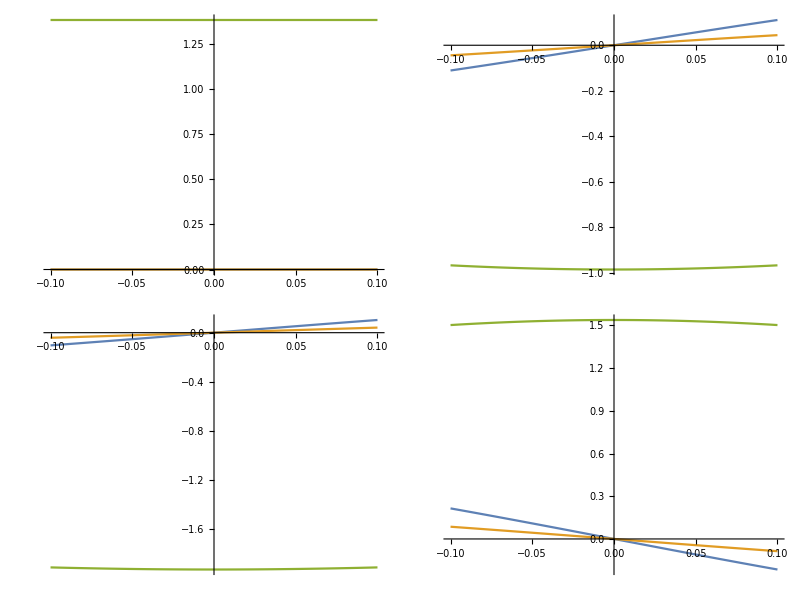

where these components go smoothly through 0 iff 0 is explicitly excluded as a point.

Note that this doesn't apply to the angle between any two vectors

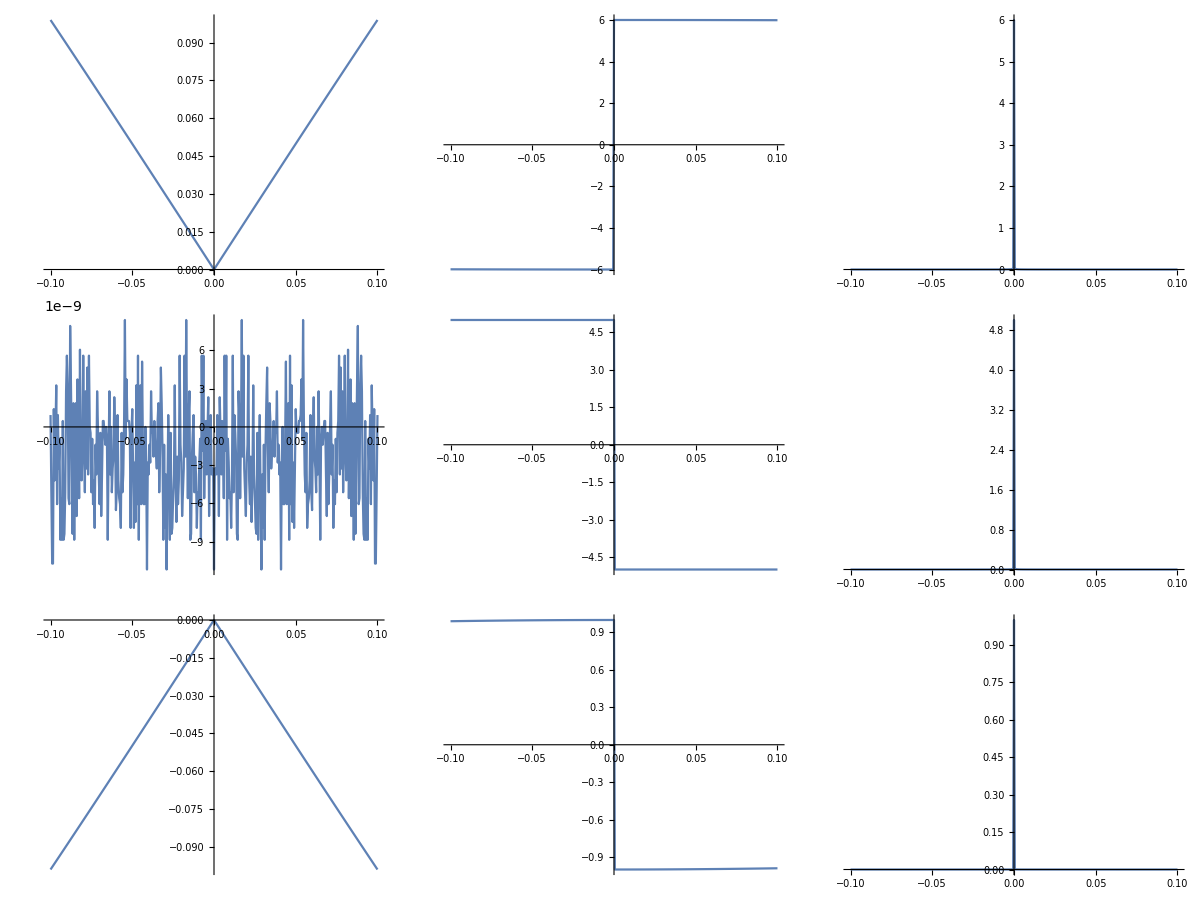

there are some clear discontinuities and turning points here. That means the appropriate limiting behavior is really coming from something about how the dihedral angle is defined...or from the fact that it takes care of any sign issues by definition? But the issue is that I’m finding that these derivatives should all be 0 at 0...

```mathematica
dihedScan=DeleteCases[#, 0.]&@Range[-.005, .005, .001];
```

```mathematica
getDihedFD[
{
{0, 0, 0},
{.5, .7, 0},
{.7, .2, 0},
{1.2, .7, 0.}
},
1,
2,
3,
4
]
```

{-1.11759×10^-8,-1.11759×10^-8,1.38081,-1.11759×10^-8,-1.11759×10^-8,-0.986294,-1.11759×10^-8,-1.11759×10^-8,-1.93314,-1.11759×10^-8,-1.11759×10^-8,1.53862}

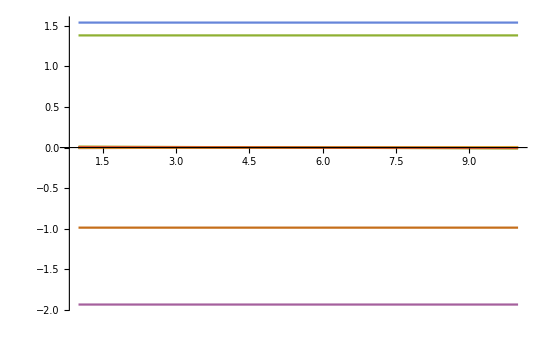

```mathematica
ListLinePlot[
Transpose@Table[
getDihedFD[
{
{0, 0, 0},
{.5, .7, 0},
{.7, .2, 0},
{1.2, .7, x}
},
1,
2,
3,
4
],
{x, dihedScan}
],
PlotRange->All
]
```

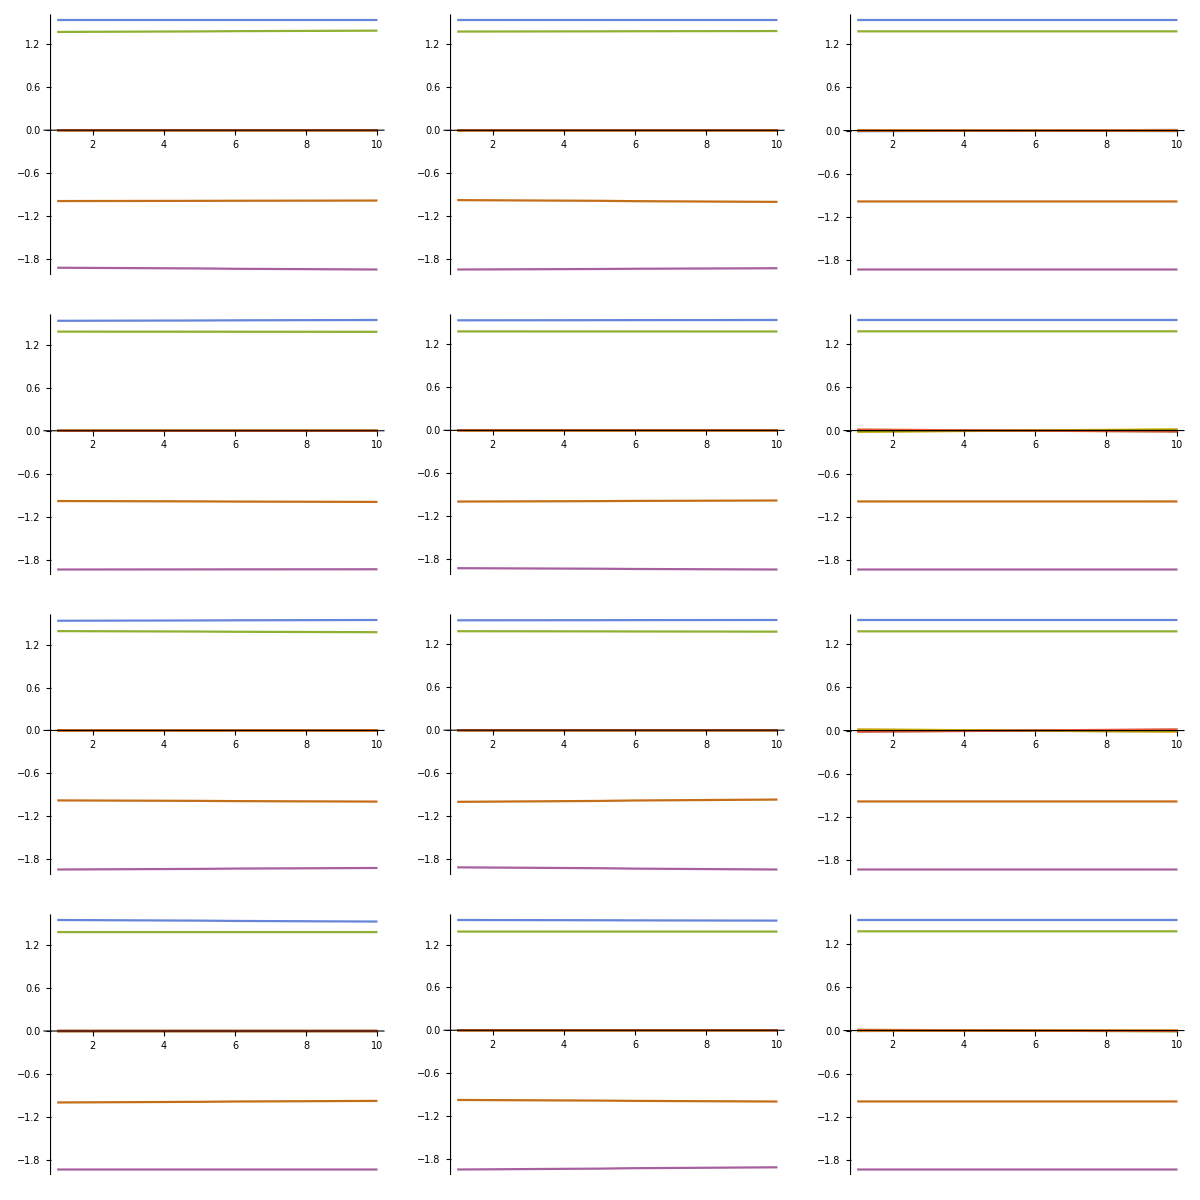

```mathematica
Table[
ListLinePlot[
Transpose@Table[
getDihedFD[
ReplacePart[#, {i, j}->#[[i, j]]+x]&@{
{0, 0, 0},
{.5, .7, 0},
{.7, .2, 0},
{1.2, .7, 0.}
},
1,
2,
3,
4
],
{x, dihedScan}
],
PlotRange->All
],
{i, 4},
{j, 3}
]//Grid
```

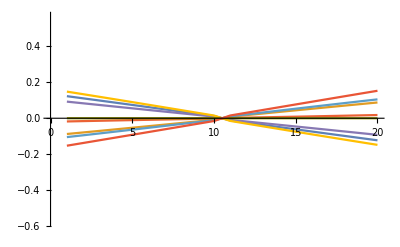

```mathematica
ListLinePlot[
Transpose@Table[
getDihedFD[
{
{0, 0, 0},
{.5, .7, 0},
{.7, .2, 0.+x},
{1.2, .7, 0.}
},
1,
2,
3,
4
],
{x, dihedScan}
]
]
```

```mathematica
Block[{d=.00005, struct, 
g=DeleteCases[#, 0.]&@Range[-.1, .1, .0005]},
Table[
ListLinePlot[
Map[Transpose[{g, #}]&]@
Table[
struct={
{0, 0, 0},
{.5, .7, 0},
{.7, .2, 0},
{1.2, .7, x}
};
({-1/2, 0, 1/2}/d).
Table[
getDihed[
ReplacePart[struct,
j->struct[[j]]+d*s*IdentityMatrix[3][[i]]
],
1,
2,
3,
4
],
{s, -1, 1} 
],
{i,3},
{x, g}
],
ImageSize->250
],
{j, 4}
]
]//Partition[#, 2]&//Grid
```

-Graphics-

##### Expanded Terms

We’re going to expand these terms as much as possible to be able to get more numerically-stable versions

(∂r_ij)/(∂x_m)=∂/(∂x_m)a · ∇_a |a|
(∂θ_ijk)/(∂x_m)=∂/(∂x_m)(a | b) · ∇_(a | b) tan^-1(sin(a, b), cos(a, b))
∂/(∂x_n)τ_ijkl=∂/(∂x_n)(n_1 | n_2)∇_(n_1 | n_2) tan^-1(sin(n_1, n_2), cos(n_1, n_2))

this will mostly be handled in the parts that aren’t just coordinate transformations

Case 1: r

∇_a |a| = â

this is stable because we can easily zero this vector out if it gets numerically problematic

Case 2: θ

∇_(a | b) tan^-1(sin(a, b), cos(a, b))=(cos(a, b)∂/(∂a)sin(a, b) - sin(a, b)∂/(∂a)cos(a, b)
cos(a, b)∂/(∂b)sin(a, b) - sin(a, b)∂/(∂b)cos(a, b))
=(1/(|a|)cos(a, b)(b̂×n̂-sin(a, b)â) - 1/(|a|)sin(a, b)(b̂-cos(a, b)â)
1/(|b|)cos(a, b)(n̂×â-sin(a, b)b̂) -1/(|b|) sin(a, b)(â-cos(a, b)b̂))

the b̂/|a| and â/|b| terms here would seem to be problematic, however they are actually okay as long as we define sin(𝟘, b)= cos(𝟘, b) = sin(a, 𝟘) = cos(a, 𝟘) = 0.

Case 3: τ

Same considerations as for θ

#### Second Derivatives

Case 1: r

Straightforward using what we know how to do from various other vector derivative work

(∂^2 r_ij)/(∂x_n∂x_m)=∂/(∂x_n)(∂/(∂x_m)a · ∇_a |a|)
=∇_(x_n x_m) a·∇_a |a| + ∇_x_n a⟨2⟩∇_x_m a∇_(a^2) |a|

expanding this in full

∇_(x_n x_m) a=∂^2/(∂x_n∂x_m)(x_j-x_i)
=𝟘
∇_x_n a⟨2⟩∇_x_m a∇_(a^2) |a|=(𝕀_3 δ_jn-𝕀_3 δ_in)⟨2⟩(𝕀_3 δ_jm-𝕀_3 δ_im)∇_(a^2) |a|
=δ_jn δ_jm∇_(a^2) |a|-δ_jn δ_im∇_(a^2) |a|-δ_in δ_jm∇_(a^2) |a|+δ_in δ_im∇_(a^2) |a|

##### Case 2: θ

∂^2/(∂x_n∂x_m)θ_ijk=∇_(x_n,x_m) (a | b)·∇_(a | b) tan^-1(sin(a, b), cos(a, b)) + ∇_x_n (a | b)⟨2⟩∇_x_m (a | b)∇_((a | b),(a | b)) tan^-1(sin(a, b), cos(a, b))

the trickiest term here is

∇_((a | b),(a | b)) tan^-1(sin(a, b), cos(a, b))

which will be a 2×2 matrix of derivative vectors where each term looks like

∂^2/(∂β∂α)θ(a, b) =∂/(∂β) (cos(a, b)∂/(∂α)sin(a, b) - sin(a, b)∂/(∂α)cos(a, b))
=∂/(∂β)cos(a, b)⊗∂/(∂α)sin(a, b)+cos(a, b)∂/(∂β∂α)sin(a, b)-∂/(∂β)sin(a, b)⊗∂/(∂α)cos(a, b)-sin(a, b)∂/(∂β∂α)cos(a, b)

or rewriting this in a not-stupid way we have

∂^2/(∂x_n∂x_m)θ_ijk=∇_(x_n,x_m) (a | b)·∇_(a | b) θ(a, b) + ∇_x_n (a | b)⟨2⟩∇_x_m (a | b)∇_((a | b)^2) θ(a, b)

and then, again by linearity

∇_(x_n,x_m) (a | b)=𝟘

so

∂^2/(∂x_n∂x_m)θ_ijk=∇_x_n (a | b)⟨2⟩∇_x_m (a | b)∇_((a | b)^2) θ(a, b)

and then writing

∇_((a | b)^2) θ(a, b)=((∂^2 θ)/(∂a∂a) | (∂^2 θ)/(∂a∂b)
(∂^2 θ)/(∂b∂a) | (∂^2 θ)/(∂b∂b))
∇_x_n (a | b)=(𝕀_3 δ_jn-𝕀_3 δ_in | 𝕀_3 δ_kn-𝕀_3 δ_in)
∇_x_n (a | b)⟨2⟩∇_x_m (a | b)∇_((a | b)^2) θ(a, b)=(𝕀_3 δ_jn-𝕀_3 δ_in | 𝕀_3 δ_kn-𝕀_3 δ_in)((∂^2 θ)/(∂a∂a)δ_jm-(∂^2 θ)/(∂a∂a)δ_im+(∂^2 θ)/(∂b∂a)δ_km-(∂^2 θ)/(∂b∂a)δ_im
(∂^2 θ)/(∂a∂b)δ_jm-(∂^2 θ)/(∂a∂b)δ_im+(∂^2 θ)/(∂b∂b)δ_km-(∂^2 θ)/(∂b∂b)δ_im)
=(∂^2 θ)/(∂a∂a)(δ_jn-δ_in)δ_jm-(∂^2 θ)/(∂a∂a)(δ_jn-δ_in)δ_im+(∂^2 θ)/(∂b∂a)(δ_jn-δ_in)δ_km-(∂^2 θ)/(∂b∂a)(δ_jn-δ_in)δ_im
+(∂^2 θ)/(∂a∂b)(δ_kn-δ_in)δ_jm-(∂^2 θ)/(∂a∂b)(δ_kn-δ_in)δ_im+(∂^2 θ)/(∂b∂b)(δ_kn-δ_in)δ_km-(∂^2 θ)/(∂b∂b)(δ_kn-δ_in)δ_im
=((∂^2 θ)/(∂a∂a)(δ_jn-δ_in)+(∂^2 θ)/(∂a∂b)(δ_kn-δ_in))δ_jm+((∂^2 θ)/(∂b∂a)(δ_jn-δ_in)+(∂^2 θ)/(∂b∂b)(δ_kn-δ_in))δ_km
-(((∂^2 θ)/(∂a∂a)+(∂^2 θ)/(∂b∂a))(δ_jn-δ_in)+((∂^2 θ)/(∂a∂b)+(∂^2 θ)/(∂b∂b))(δ_kn-δ_in))δ_im

and splitting this into its δ-terms we have a 3×3 matrix like

((∂^2 θ)/(∂a∂a)+(∂^2 θ)/(∂b∂a)+(∂^2 θ)/(∂a∂b)+(∂^2 θ)/(∂b∂b))δ_in δ_im | -((∂^2 θ)/(∂a∂a)+(∂^2 θ)/(∂a∂b))δ_in δ_jm | -((∂^2 θ)/(∂b∂a)+(∂^2 θ)/(∂b∂b))δ_in δ_km
-((∂^2 θ)/(∂a∂a)+(∂^2 θ)/(∂b∂a))δ_jn δ_im | (∂^2 θ)/(∂a∂a)δ_jn δ_jm | (∂^2 θ)/(∂b∂a)δ_jn δ_km
-((∂^2 θ)/(∂a∂b)+(∂^2 θ)/(∂b∂b))δ_kn δ_im | (∂^2 θ)/(∂a∂b)δ_kn δ_jm | (∂^2 θ)/(∂b∂b)δ_kn δ_km

Case 3: τ

sgn(b̂·((n̂)_1×(n̂)_2))∂/(∂x_n)τ_ijkl=∂/(∂x_n)(a | b | c) · ∇_(a | b | c) (n_1 | n_2) · ∇_(n_1 | n_2) tan^-1(sin(n_1, n_2), cos(n_1, n_2))
=∂/(∂x_n)(n_1 | n_2)∇_(n_1 | n_2) tan^-1(sin(n_1, n_2), cos(n_1, n_2))

and so this will actually looks basically identical to the θ case, and again we have linear relationships between x and a/b/c so

∂^2/(∂x_n∂x_m)τ_ijkl=∇_x_n (n_1 | n_2)⟨2⟩∇_x_m (n_1 | n_2)∇_((n_1 | n_2)^2) θ(n_1, n_2)

This is gonna get nasty quick, of course, when we note that we have

∇_x_m (n_1 | n_2)=((𝕀_3×b)(δ_mj-δ_mi) + (a×𝕀_3)(δ_mk-δ_mj) | (𝕀_3×c)(δ_mk-δ_mj) + (b×𝕀_3)(δ_ml-δ_mk))
=((-ϵ_3b)(δ_mj-δ_mi) + (ϵ_3 a)(δ_mk-δ_mj) | (-ϵ_3c)(δ_mk-δ_mj) + (ϵ_3 b)(δ_ml-δ_mk))

so we’ll write

∇_((n_1 | n_2)^2) θ(n_1, n_2)=(θ^11 | θ^12
θ^21 | θ^22)
∇_x_m (n_1 | n_2)=(C_b^i-C_b^j+C_a^k-C_a^j | C_c^j-C_c^k+C_b^l-C_b^k)
=(C_b^i+C_a^k-C_(a+b)^j | C_c^j+C_b^l-C_(b+c)^k)

where

C_(a+b)=C_a+C_b
C_(b+c)=C_b+C_c

you’ll note we’ve lost the m index—this is intentional. Now we have

∇_x_n (n_1 | n_2)⟨2⟩∇_x_m (n_1 | n_2)∇_((n_1 | n_2)^2) θ(n_1, n_2)=∇_x_n (n_1 | n_2)((C_b^i+C_a^k-C_(a+b)^j)θ^11+(C_c^j+C_b^l-C_(b+c)^k)θ^21
(C_b^i+C_a^k-C_(a+b)^j)θ^12+(C_c^j+C_b^l-C_(b+c)^k)θ^22)
=(C_b^i+C_a^k-C_(a+b)^j | C_c^j+C_b^l-C_(b+c)^k)((C_b^i+C_a^k-C_(a+b)^j)θ^11+(C_c^j+C_b^l-C_(b+c)^k)θ^21
(C_b^i+C_a^k-C_(a+b)^j)θ^12+(C_c^j+C_b^l-C_(b+c)^k)θ^22)
=(C_b^i+C_a^k-C_(a+b)^j)((C_b^i+C_a^k-C_(a+b)^j)θ^11+(C_c^j+C_b^l-C_(b+c)^k)θ^21)
+(C_c^j+C_b^l-C_(b+c)^k)((C_b^i+C_a^k-C_(a+b)^j)θ^12+(C_c^j+C_b^l-C_(b+c)^k)θ^22)

and the reason I dropped the m and n indices is that this makes it easier to partition as a 4×4 given by the terms

(δ_ni δ_mi | δ_ni δ_mj | δ_ni δ_mk | δ_ni δ_ml
δ_nj δ_mi | δ_nj δ_mj | δ_nj δ_mk | δ_nj δ_ml
δ_nk δ_mi | δ_nk δ_mj | δ_nk δ_mk | δ_nk δ_ml
δ_nl δ_mi | δ_nl δ_mj | δ_nl δ_mk | δ_nl δ_ml)

so now doing that expansion (I actually did it in Mathematica...) we get

```mathematica
With[{i=i,j=j,k=k,a=a, b=b, c=c,θ=θ, i2=n[1], i1=n[2]},
delXN[n_]:= {C[n, b, i]+C[n, a, k]-C[n, a+b, j], C[n, c, j]+C[n, b,l]-C[n, b+c, k]};
q2 = Array[θ, {2, 2}];
terms=Expand[delXN[i2].(delXN[i1].q2)];
termMatrix=
Table[
Select[terms,MemberQ[#, C[i2,_, α], Infinity]&&MemberQ[#, C[i1, _, β], Infinity]&]//Simplify,
{α, {i, j, k, l}},
{β, {i, j, k, l}}
];
formmattedTermMat=Map[HoldForm, termMatrix, {2}]/.{
i2->n,
i1->m
}//ReplaceAll[{
C[n_, a_, i_]:>Subsuperscript["C", a, Row@{i,n}],
θ[a_, b_]:>Superscript["θ", Row@{a, b}]
}];
];
```

```mathematica
formmattedTermMat//MatrixForm
```

(C_b^in C_b^im θ^11 | C_b^in (-C_(a+b)^jm θ^11+C_c^jm θ^21) | C_b^in (C_a^km θ^11-C_(b+c)^km θ^21) | C_b^in C_b^lm θ^21
C_b^im (-C_(a+b)^jn θ^11+C_c^jn θ^12) | C_(a+b)^jn (C_(a+b)^jm θ^11-C_c^jm θ^21)+C_c^jn (-C_(a+b)^jm θ^12+C_c^jm θ^22) | C_(a+b)^jn (-C_a^km θ^11+C_(b+c)^km θ^21)+C_c^jn (C_a^km θ^12-C_(b+c)^km θ^22) | C_b^lm (-C_(a+b)^jn θ^21+C_c^jn θ^22)
C_b^im (C_a^kn θ^11-C_(b+c)^kn θ^12) | C_a^kn (-C_(a+b)^jm θ^11+C_c^jm θ^21)+C_(b+c)^kn (C_(a+b)^jm θ^12-C_c^jm θ^22) | C_a^kn (C_a^km θ^11-C_(b+c)^km θ^21)+C_(b+c)^kn (-C_a^km θ^12+C_(b+c)^km θ^22) | C_b^lm (C_a^kn θ^21-C_(b+c)^kn θ^22)
C_b^ln C_b^im θ^12 | C_b^ln (-C_(a+b)^jm θ^12+C_c^jm θ^22) | C_b^ln (C_a^km θ^12-C_(b+c)^km θ^22) | C_b^ln C_b^lm θ^22)

(C_b C_b θ^11 | C_b C_c θ^21-C_b C_(a+b)θ^11 | C_b C_a θ^11-C_b C_(b+c)θ^21 | C_b C_b θ^21
C_c C_b θ^12-C_(a+b)C_b θ^11 | C_(a+b)C_(a+b)θ^11-C_(a+b)C_c θ^21-C_c C_(a+b)θ^11+C_c C_c θ^22 | C_(a+b)C_(b+c)θ^21-C_c C_(b+c)θ^22-C_(a+b)C_a θ^11+C_c C_a θ^12 | C_c C_b θ^22-C_(a+b)C_b θ^21
C_a C_b θ^11-C_(b+c)C_b θ^12 | C_(b+c)C_(a+b)θ^12-C_(b+c)C_c θ^22-C_a C_(a+b)θ^11+C_a C_c θ^21 | C_a C_a θ^11-C_a C_(b+c)θ^21-C_(b+c)C_a θ^12+C_(b+c)C_(b+c)θ^22 | C_a C_b θ^21-C_(b+c)C_b θ^22
C_b C_b θ^12 | C_b C_c θ^22-C_b C_(a+b)θ^12 | C_b C_a θ^12-C_b C_(b+c)θ^22 | C_b C_b θ^22)

##### Expanded Terms

Case 1: r

∇_(a^2) |a| = 1/(|a|)(𝕀_3-â⊗â)

This can get potentially nasty since we have that 1/(|a|)𝕀_3 term...we’ll need to be cognizant of that

Case 2: θ

We’ve got four forms coming from

∂^2/(∂β∂α)θ(a, b) =∂/(∂β) (cos(a, b)∂/(∂α)sin(a, b) - sin(a, b)∂/(∂α)cos(a, b))
=∂/(∂β)cos(a, b)∂/(∂α)sin(a, b)+cos(a, b)∂/(∂β∂α)sin(a, b)-∂/(∂β)sin(a, b)∂/(∂α)cos(a, b)-sin(a, b)∂/(∂β∂α)cos(a, b)

and...actually I think none of these will necessarily be problematic either? Lots of zeros. Maybe enough zeros?

#### Implementation

Test implementations

```mathematica
testCoords=;
testCoordsSpec=;
```

##### Analytic

Angles

```mathematica
sinCosDeriv[coords_, i_, j_, k_]:=
Block[{a, b},
a=coords[[j]] - coords[[i]];
b=coords[[k]]-coords[[i]];

]
```

##### FD

Distances

```mathematica
getDist[coords_, i_, j_]:=
Norm[coords[[j]]-coords[[i]]];
getDist[i_, j_][coords_]:=
getDist[coords, i, j];
```

Angles

```mathematica
Clear[getAngleComponents, getAngle]
getAngleComponents[coords_, i_, j_, k_]:=
Block[
{
a = coords[[j]]-coords[[i]],
b = coords[[k]]-coords[[i]],
sin,
cos
},
sin=Norm[Cross[a, b]]/(Norm[a]*Norm[b]);
cos=Dot[a, b]/(Norm[a]*Norm[b]);
{sin, cos, ArcTan[cos, sin]}
];
getAngle[coords_, i_, j_, k_]:=
getAngleComponents[coords, i, j, k][[-1]];
getAngle[i_, j_, k_][coords_]:=
getAngle[coords, i, j, k];
```

```mathematica
Clear[getCosFD, getCosFD, getAngleFD];
getSinFD[coords_, i_, j_, k_, dx_:.0000001]:=
Table[
NDSolve`FiniteDifferenceDerivative[
1,
Sequence@@
Transpose@Table[
{
dx*a,
getAngleComponents[
coords+
ReplacePart[ConstantArray[0., Dimensions[coords]],
{n, m}->dx*a
],
i, j, k
][[1]]
},
{a, -5, 5, 1}
]
][[2]],
{n, Dimensions[coords][[1]]},
{m, Dimensions[coords][[2]]}
]//Flatten;
getCosFD[coords_, i_, j_, k_, dx_:.0000001]:=
Table[
NDSolve`FiniteDifferenceDerivative[
1,
Sequence@@
Transpose@Table[
{
dx*a,
getAngleComponents[
coords+
ReplacePart[ConstantArray[0., Dimensions[coords]],
{n, m}->dx*a
],
i, j, k
][[2]]
},
{a, -5, 5, 1}
]
][[2]],
{n, Dimensions[coords][[1]]},
{m, Dimensions[coords][[2]]}
]//Flatten;
getAngleFD[coords_, i_, j_, k_,  dx_:.0000001]:=
Table[
NDSolve`FiniteDifferenceDerivative[
1,
Sequence@@
Transpose@Table[
{
dx*a,
getAngle[
coords+
ReplacePart[ConstantArray[0., Dimensions[coords]],
{n, m}->dx*a
],
i, j, k
]
},
{a, -5, 5, 1}
]
][[2]],
{n, Dimensions[coords][[1]]},
{m, Dimensions[coords][[2]]}
]//Flatten
```

```mathematica
getSinFD[testCoords, 2 ,3 ,1][[;;9]]//MatrixForm
```

(0.564035
-0.156037
0.609499
0.761207
-0.148314
-0.806884
-1.32524
0.304351
0.197384)

```mathematica
getCosFD[testCoords, 2 ,3 ,1][[;;9]]//MatrixForm
```

(-0.789896
0.21852
-0.853566
-1.06602
0.207705
1.12999
1.85592
-0.426225
-0.276424)

```mathematica
getAngleFD[testCoords, 2 ,3 ,1][[;;9]]//MatrixForm
```

(0.970603
-0.268512
1.04884
1.3099
-0.255223
-1.3885
-2.2805
0.523734
0.339663)

FD Diheds

```mathematica
getDihedBits[coords_, i_, j_, k_, l_]:=
Block[
{
a = coords[[j]]-coords[[i]],
b = coords[[k]]-coords[[j]],
c = coords[[l]]-coords[[k]],
axb,
bxc,
n,
d1, 
d2
},
axb=Cross[a, b]//Normalize;
bxc=Cross[b, c]//Normalize;
n=Cross[Normalize[b], axb];
{axb, bxc, n}
]
getDihed[coords_, i_, j_, k_, l_]:=
Block[
{
axb,
bxc,
n,
d1, 
d2
},
{axb, bxc, n}=getDihedBits[coords, i, j, k, l];
ArcTan[Dot[axb, bxc], Dot[n, bxc]]
];
getDihed[i_, j_, k_, l_][coords_]:=
getDihed[coords, i, j, k, l];
```

```mathematica
Clear[getDihedFD];
getDihedFD[coords_, i_, j_, k_, l_,  dx_:.0000001, s_:5]:=
Table[
NDSolve`FiniteDifferenceDerivative[
1,
Sequence@@
Transpose@Table[
{
dx*a,
getDihed[
coords+
ReplacePart[ConstantArray[0., Dimensions[coords]],
{n, m}->dx*a
],
i, j, k, l
]
},
{a, -s, s, 1}
]
][[2]],
{n, Dimensions[coords][[1]]},
{m, Dimensions[coords][[2]]}
]//Flatten;
```

```mathematica
getAngleFD[testCoords, 2 ,3 ,1][[;;9]]
```

```mathematica
Block[{getDihed=With[{b=getDihedBits[##]}, ArcTan@Dot[b[[1]], b[[2]]]]&},
getDihedFD[ochhCoords, 4, 2, 1, 3, 1*^-8, 7]//Partition[#, 3]&//Threshold
]//MatrixForm
```

(2.32831×10^-8 | -6.51926×10^-9 | -6.51926×10^-9
-7.54371×10^-8 | -6.51926×10^-9 | -6.51926×10^-9
-6.51926×10^-9 | -6.51926×10^-9 | -6.51926×10^-9
-6.51926×10^-9 | -6.51926×10^-9 | -6.51926×10^-9)

```mathematica
With[{b=getDihedBits[ochhCoords, 4, 2, 1, 3]}, 
{b[[3]], b[[2]]}
]
```

{{1.22465×10^-16,1.,3.41132×10^-31},{-1.,-2.67956×10^-31,-2.55849×10^-31}}

```mathematica
rooop=RotationMatrix[RandomReal[{0, 2π}], {{1, 0, 0}, RandomReal[{}, {3}]}];
```

```mathematica
rooop
```

{{0.232491,-0.873639,-0.427438},{0.873639,0.380729,-0.302985},{0.427438,-0.302985,0.851761}}

```mathematica
Block[{getDihed=With[{b=getDihedBits[##]}, Dot[b[[1]], b[[2]]]*Dot[b[[3]], b[[2]]]]&},
getDihedFD[ochhCoords.rooop, 4, 2, 1, 3, 1*^-5, 3]//Partition[#, 3]&//Threshold
]//MatrixForm
```

(-0.123913 | 0.465625 | 0.227817
0.383942 | -1.44277 | -0.705878
-0.130019 | 0.488573 | 0.239036
-0.130014 | 0.488564 | 0.239039)

```mathematica
getDihedFD[ochhCoords.rooop, 4, 2, 1, 3, 1*^-5, 12]//Partition[#, 3]&//Threshold//MatrixForm
```

(-0.123917 | 0.465614 | 0.227832
0.383929 | -1.44281 | -0.705832
-0.130031 | 0.488591 | 0.239029
-0.130003 | 0.488546 | 0.239047)

```mathematica
Block[{getDihed=With[{b=getDihedBits[##]}, Dot[b[[3]], b[[2]]]]&},
getDihedFD[ochhCoords, 4, 2, 1, 3, 1*^-5, 12]//Partition[#, 3]&//Threshold
]//MatrixForm
```

(0.532975 | 0. | 0.
-1.65144 | 0. | 0.
0.559234 | 0. | 0.
0.559234 | 0. | 0.)

```mathematica
Block[{getDihed=With[{b=getDihedBits[##]}, ArcTan@Dot[b[[3]], b[[2]]]]&},
getDihedFD[ochhCoords, 4, 2, 1, 3, 1*^-5, 12]//Partition[#, 3]&//Threshold
]//MatrixForm
```

(0.532975 | 0. | 0.
-1.65144 | 0. | 0.
0.559234 | 0. | 0.
0.559234 | 0. | 0.)

```mathematica
getDihedFD[ochhCoords, 4, 2, 1, 3, 1*^-5, 12]//Partition[#, 3]&//Threshold//MatrixForm
```

(-0.532975 | 0. | 0.
1.65144 | 0. | 0.
-0.559234 | 0. | 0.
-0.559234 | 0. | 0.)

```mathematica
ochhCoords[[4]]-ochhCoords[[2]]//Norm
```

2.10043

```mathematica
ochhCoords[[3]]-ochhCoords[[1]]//Norm
```

3.85433

```mathematica
ochhCoords//Threshold//MatrixForm
```

(0. | 0. | 1.29398
0. | 0. | -1.0185
0. | 1.78816 | -2.12045
0. | -1.78816 | -2.12045)

## Useful Identities

Here are a list of useful transformations, esp. useful when implementing. We’ll assume a and b are vectors that don’t depend on one another

#### Dot Product

∂/(∂a)a·b=(∂a)/(∂a)·b
=𝕀_3·b
=b

#### Vector Norm

∂/(∂a)|a|=∂/(∂a)√(a·a)
=1/(2|a|)∂/(∂a)a·a
=1/(|a|)(∂a)/(∂a)·a
=1/(|a|)𝕀_3 a
=a/(|a|)
=â

although there is one subtlety when all of the elements are zero, because we end up with a bunch of 0/0 terms and we need to decide what they are. This is formally indeterminate but we will choose the convention that it is zero.

#### Normalized Vector (Vector Norm 2nd Derivative)

(∂â)/(∂a)=∂/(∂a)a/(|a|)
=-1/(|a|)^2((∂|a|)/(∂a)⊗a)+1/(|a|)(∂a)/(∂a)
=1/(|a|)(𝕀_3-a/(|a|)⊗a/(|a|))
=1/(|a|)(𝕀_3-â⊗â)

#### Cross Product Norm

∂/(∂a)|a×b|=∂/(∂a)√((a×b)·(a×b))
=1/(|a×b|)(∂/(∂a)(a×b))·(a×b)
=1/(|a×b|)((∂a)/(∂a)×b)·(a×b)
=1/(|a×b|)(𝕀_3×b)(a×b)
=-((ϵ_3 b)(a×b))/(|a×b|)
 =(b×(a×b))/(|a×b|)
=1/(|a×b|)(a(b·b) - b(a·b))
=1/(|a||b|sinθ)(a(|b|)^2 - b |a||b|cosθ)
=â|b|cscθ - b tanθ

## Angle Derivatives

Derivatives of sines and cosines between vectors keep coming up, so we’ll address them on their own. To start, we have

sin(a, b) = (|a×b|)/(|a||b|)
cos(a, b) = (a·b)/(|a||b|)

and we’ll also want to get derivatives of things like

θ(a, b) = tan^-1(sin(a, b), cos(a, b))

#### First Derivatives

##### Sin/Cos

We’ll expand the derivatives through the product rule

∂/(∂a)sin(a, b) =1/(|a||b|)∂/(∂a)|a×b|-(|a×b|)/(|a||b|)^2|b|∂/(∂a)|a|
=1/(|a||b|)∂/(∂a)|a×b|-sin(a, b)1/(|a|)∂/(∂a)|a|
∂/(∂a)cos(a, b) =1/(|a||b|)∂/(∂a)a·b-(a·b)/(|a||b|)^2|b|∂/(∂a)|a|
=1/(|a||b|)(∂/(∂a)a·b-cos(a, b)|b|∂/(∂a)|a|)

then we rewrite the norms like

∂/(∂a)|a|=∂/(∂a)√(a·a) | ∂/(∂a)|a×b|=∂/(∂a)√((a×b)·(a×b)) | ∂/(∂a)a·b=(∂a)/(∂a)·b
=1/(2|a|)∂/(∂a)a·a | =1/(|a×b|)(∂/(∂a)(a×b))·(a×b) | =𝕀_3·b
=1/(|a|)(∂a)/(∂a)·a | =1/(|a×b|)((∂a)/(∂a)×b)·(a×b) | =b
=1/(|a|)𝕀_3 a | =1/(|a×b|)(𝕀_3×b)(a×b) |  
=a/(|a|) | =-((ϵ_3 b)(a×b))/(|a×b|) |  
  |  =(b×(a×b))/(|a×b|) |

giving us

∂/(∂a)sin(a, b) =1/(|a|)(b̂×n̂-sin(a, b)â)
∂/(∂a)cos(a, b) =1/(|a|)(b̂-cos(a, b)â)

and then for the other direction (not certain this is written right)

∂/(∂b)sin(a, b) =1/(|a||b|)(∂/(∂b)|a×b|-sin(a, b)∂/(∂b)|b|)
∂/(∂b)cos(a, b) =1/(|a||b|)(∂/(∂b)a·b-cos(a, b)|a|∂/(∂b)|b|)

and 90% of this is identical to the other direction, but we need to worry about commutativity so

∂/(∂b)|a×b|=∂/(∂b)√((a×b)·(a×b))
=1/(|a×b|)(∂/(∂b)(a×b))·(a×b)
=1/(|a×b|)(a×∂/(∂b))·(a×b)
=(a×∂/(∂b))·(a×b)
=((ϵ_3 a)(a×b))/(|a×b|)
=((a×b)×a)/(|a×b|)

and then we get

∂/(∂a)sin(a, b) =1/(|a|)(b̂×n̂-sin(a, b)â)
∂/(∂a)cos(a, b) =1/(|a|)(b̂-cos(a, b)â)
∂/(∂b)sin(a, b) =1/(|b|)(n̂×â-sin(a, b)b̂)
∂/(∂b)cos(a, b) =1/(|b|)(â-cos(a, b)b̂)

we’ll note one thing that might be useful from some triple-product properties:

b̂×n̂=1/(|n|)b̂×(a×b)
=1/(|n|)(b̂·a)b-(b̂·b)a
=1/(|n|)(b̂·a)b-|b|a
=1/(|n|)(cos(a, b)|a|b - |b|a)

There are a few notable things about these definitions. First off, looking at the cos definitions they look are symmetric with respect to the order in which the vectors are supplied. This is consistent with the fact that cos is an even function. We’ll assume for now that we’re taking the derivative with respect to b. So when we look at the derivative vector, it points in the direction of â, but then subtracts off the component in b̂, but scaled by the cos of the angle between the vectors. Note that this is identical to what is done in a Gram-Schmidt orthogonalization, assuming unit vectors.

Next for the sine functions we see that we have a cross product term. This term gives us something that is perpendicular to both the vector normal to the ab plane and the b vector, which is to say if a and b are perpendicular, this points in the direction of a. This then has the component along b subtracted off, but scaled by the sin of the angle between the two. This seems like it won’t exactly have a nice geometric meaning, but we can actually note something special here. First off, we recall that for real numbers

cos(θ)=sin(θ-π/2)

and then we let

θ=∠(â, b̂)=arccos(â·b̂)
φ=∠(â×n̂, b̂)

and then we note that

φ=π/2-θ

Graphically we can see this from

```mathematica
Block[{a, b, n, c, θ, φ},
BlockRandom[
SeedRandom[20];
a={1., 0., 0.};
b=Normalize@Append[RandomReal[{}, 2], 0.];
n=Normalize@Cross[a, b];
c=Cross[n, a];
θ=VectorAngle[a, b];
φ=VectorAngle[c,b];
Graphics3D[
{
AbsoluteThickness[1.5],
Red,
Text[Style["â", FontSize->15], RotationMatrix[π/24, n].a/2],
Arrow[{{0, 0, 0}, a}],
Blue,
Text[Style["b̂", FontSize->15], RotationMatrix[π/24, n].b/2],
Arrow[{{0, 0, 0}, b}],
Darker@Green,
Text[Style["n̂", FontSize->15], RotationMatrix[π/24, Cross[n, b]].n/2],
Arrow[{{0, 0, 0}, n}],
Purple,
Text[Style["n̂×â", FontSize->15], RotationMatrix[-π/24, n].c/1.5],
Arrow[{{0, 0, 0}, c}],
Black,
Text[Style["θ", FontSize->15], RotationMatrix[θ/2, n].a/4],
Line[Table[RotationMatrix[τ, n].a/5, {τ, 0., θ, θ/24}]],
Text[Style["φ",FontSize->15], RotationMatrix[φ/2, n].b/3],
Line[Table[RotationMatrix[τ, n].b/4, {τ, 0., φ, φ/24}]]
}
]
]
]
```

-Graphics3D-

Therefore we actually have

∂/(∂b)sin(a, b) =1/(|b|)(n̂×â-sin(a, b)b̂)
=1/(|b|)(n̂×â-cos(n×a, b)b̂)

and we find that the sin derivative points in the direction of n̂×â, but with the component along the direction of b̂ removed.

##### Angles

Moving to the angle derivative, it turns out the form is the same regardless of whether we take the derivative with respect to a or b, so we’ll take it relative to α∈{a, b}

∂/(∂α)θ(a, b) =∂/(∂α)tan^-1(sin(a, b), cos(a, b))
=cos(a, b)∂/(∂α)sin(a, b) - sin(a, b)∂/(∂α)cos(a, b)

and look how easy this is with everything else we’ve done!

We can however explicitly expand this out to give

∂/(∂a)θ(a, b) = cos(a, b)1/(|a|)(1/(|b||a×b|)b×(a×b)-sin(a, b)â) - sin(a, b)1/(|a|)(b̂-cos(a, b)â)
= (cos(a, b))/(|a||b||a×b|)b×(a×b) - sin(a, b)1/(|a||b|)b

and by the triple product

b×(a×b) = a(|b|)^2 - b |a||b| cos(a, b)

so

∂/(∂a)θ(a, b) = (cos(a, b))/(|a||b||a×b|)a (|b|)^2 - (cos(a, b))^2/(|a×b|)b - (sin(a, b))^2/(|a×b|)b
=1/(|a×b|)(cos(a, b)|b| â - b)

and by similar arguments we get

∂/(∂b)θ(a, b) = 1/(|a×b|)(cos(a, b)|a|b̂ - a)

or to provide a bit of intuition, maybe, we can rewrite this as

(∂θ)/(∂a) =-1/(|a||â×b̂|)(b̂-(â·b̂)â)
(∂θ)/(∂b) =-1/(|b||â×b̂|)(â-(â·b̂)b̂)

where b̂-(â·b̂)â is the component of b̂ perpendicular to â and similarly â-(â·b̂)b̂ is the component of â perpendicular to b̂. But by the way sin(a, b) and cos(a, b) are defined this actually gives us

|b̂-(â·b̂)â| = sin(a,b) = |â×b̂|

(∂θ_ijk)/(∂x_m)=∂/(∂x_m)(a | b) · ∇_(a | b) tan^-1(sin(a, b), cos(a, b))

and so

(∂θ)/(∂a) =-((ĉ)_a)/(|a|)
(∂θ)/(∂b) =-((ĉ)_b)/(|b|)
c_a= b̂-(â·b̂)â
c_b= â-(â·b̂)b̂

...which is actually super intuitive. The change points along the transverse direction to the vector...huh cool

We can then include the displacements to give

∂/(∂x_n)(a | b)=((∂(x_j-x_i))/(∂x_n) | (∂(x_k-x_i))/(∂x_n))
=(𝕀_3(δ_nj-δ_ni) | 𝕀_3(δ_nk-δ_ni))

and then we have ...

Viz

Or in a 2D picture

```mathematica
plotVectorAngleDerivs//Clear
plotVectorAngleDerivs[aVec_,bVec_, ops:OptionsPattern[]]:=
Block[{a,b,ca,cb, q,na, nb},
na=Norm[aVec];
a=aVec/na;
nb=Norm[bVec];
b=bVec/nb;
q=VectorAngle[a, b];
ca=b-Dot[a, b]*a//Normalize;
cb=a-Dot[a, b]*b//Normalize;
Graphics3D[
{
{
Red,
Arrow[{{0, 0, 0}, aVec}]
(*Dotted, Black,
Arrow[{{0, 0, 0}, Sin[q]*a}]*)
},
{
Blue,
Arrow[{{0, 0, 0}, bVec}]
(*Dotted,Black,
Arrow[{{0, 0, 0}, Sin[q]*b}]*)
},
{
Dotted,Red,
Arrow[{aVec, aVec- ca/na}]
},
{
Dotted,Blue,
Arrow[{bVec, bVec - cb/nb}]
}
},
ops
]
];
BlockRandom[
SeedRandom[2];
plotVectorAngleDerivs[RandomReal[{}, 3],Normalize@RandomReal[{}, 3]]
]
```

-Graphics3D-

but then what happens when the vectors go parallel? The term won’t blow up, but the limit depends on the direction chosen...

```mathematica
Block[{a=Append[1.2*Normalize@RandomReal[{}, 2], 0.]},
Table[
plotVectorAngleDerivs[a, RotationMatrix[q, {0, 0, 1}].a,
PlotRange->2{{-1, 1}, {-1, 1}, {-1, 1}}
],
{q, π/100, 2π, π/100}
]
]//ListAnimate
```

but...I think there’s something off on this analysis since FD puts these derivatives being non-zero much of the time... (notice how the following plots go smoothly through zero)

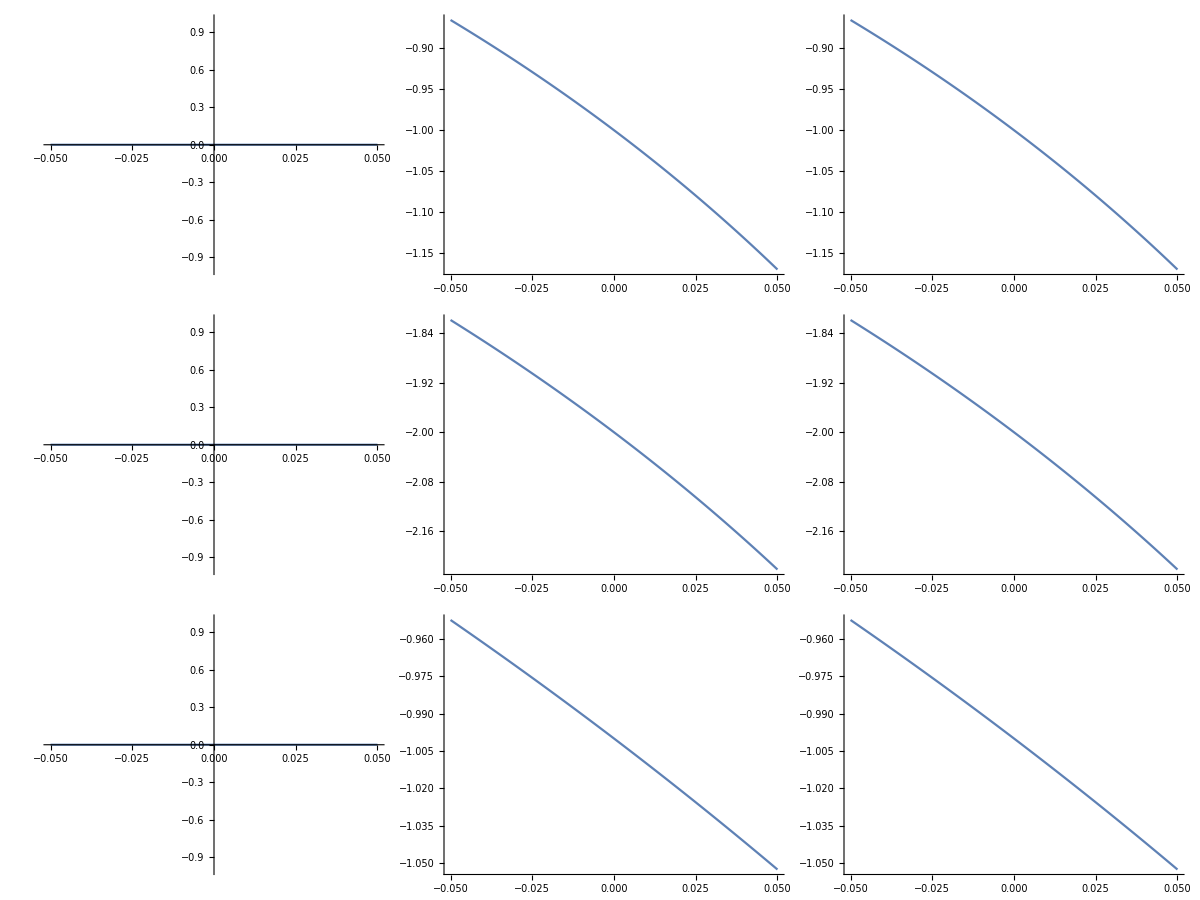
-Graphics- | -Graphics3D-

```mathematica
Grid@{{
Block[{struct, g=Range[-5*^-2, 5.0*^-2, 5.0*^-4]},
Table[
struct={
{-.5+x, .7, 0},
{0, .7, 0},
{.5, .7, 0}
};
Partition[
getAngleFD[
struct,
1,
2,
3,
1.0*^-6
],
3
],
{x, g}
]//Transpose[#, {3, 1, 2}]&
//Map[ListLinePlot[Transpose[{g, #}], ImageSize->220]&, #, {2}]&//Grid
],
{
{Red, Point[{0, .7, 0}]},
Arrow[{{.0, .7, 0}, {-.5, .7, 0}}],
Arrow[{ {.0, .7, 0}, {.5, .7, 0}}]
}//Graphics3D[#, ImageSize->500]&
}}
```

the way around this is to note that even though the derivative is ill-defined directly at 0 we should be able to get consistent results by picking a side to take the limit from and going with that (my current FD implementation seems to choose the left) for properly continuous functions the choice of side should be irrelevant one phase considerations are handled

We’ll mostly need this for derivatives of terms with respect to coordinates, so let’s imagine we do the FD there, giving us, e.g. adding ϵ to one of the components of x_i

a = x_i - x_j + ϵ δ_x
= α + ϵ δ_x
b = x_k - x_j

where

c_α= b̂-(α̂·b̂)α̂ = 0

now instead we have

c_a= b̂-(â·b̂)â
= b̂-((α+ϵ δ_im)/(|a|)·b̂)(α+ϵ δ_im)/(|a|)
= b̂-(α/(|a|)·b̂)α/(|a|) - (α/(|a|)·b̂)ϵδ_im/(|a|) - ((ϵ δ_im)/(|a|)·b̂)α/(|a|) - ((ϵ δ_im)/(|a|)·b̂)(ϵ δ_im)/(|a|)

then we’ll write

k=(|α|)/(|a|)= (|α|)/(|α+ϵ δ_im|) ⇒ |a| = (|α|)/k

so

c_a = b̂ -k^2(α̂·b̂)α̂ - (α/(|a|)·b̂)ϵδ_x/(|a|) - ((ϵ δ_x)/(|a|)·b̂)α/(|a|) - ((ϵ δ_x)/(|a|)·b̂)(ϵ δ_x)/(|a|)
= (1-k^2)(α̂·b̂)α̂ - k(α̂·b̂)ϵδ_x/(|a|)- k((ϵ δ_x)/(|a|)·b̂)α̂ - ((ϵ δ_x)/(|a|)·b̂)(ϵ δ_im)/(|a|)

and then expanding more

k = √((α_x^2+α_y^2+α_z^2)/((α_x+ϵ)^2+α_y^2+α_z^2))

so

-k(α̂·b̂)ϵδ_x/(|a|)- k((ϵ δ_im)/(|a|)·b̂)α̂ = -ϵk/(|a|)(α̂·(b̂)_x)ϵδ_x- k((ϵ δ_im)/(|a|)·b̂)α̂

meaning

c_a= b̂-(â·b̂)â
= x_i- x_j + ϵ δ_im

(∂θ)/(∂a) =-((ĉ)_a)/(|a|)
(∂θ)/(∂b) =-((ĉ)_b)/(|b|)
c_a= b̂-(â·b̂)â
c_b= â-(â·b̂)b̂

a = x_i + ϵ δ_im - x_j

∂/(∂x_m)θ = ∂/(∂a)

Implementation

```mathematica
Clear[testAngleDerivs2, testAngleDerivComps];
testAngleDerivComps[aVec_, bVec_]:=
Block[{a,b,ca,cb, da, db, na, nb},
na=Norm[aVec];
a=aVec/na;
nb=Norm[bVec];
b=bVec/nb;
ca=b-Dot[a, b]*a//Normalize;
cb=a-Dot[a, b]*b//Normalize;
da = -ca/na;
db = -cb/nb;
{da, db}
];
testAngleDerivs2[coords_, i_, j_, k_, 
zeroCutoff_:1.*^-8, 
meshSpacing_:1.*^-6, 
side_:Left]:=
Block[{aVec, bVec, a,b, da, db},
aVec=coords[[j]]-coords[[i]];
bVec=coords[[k]]-coords[[i]];
If[TrueQ[Norm[Cross[aVec, bVec]] < zeroCutoff],
Table[
aVec=
(
coords[[j]]+
If[n==2,
If[side===Left, -1, 1]*meshSpacing*IdentityMatrix[3][[m]], 
0.
]
)-(
coords[[i]]+
If[n==1,
If[side===Left, -1, 1]*meshSpacing*IdentityMatrix[3][[m]], 
0.
]
);
bVec=(
coords[[k]]+
If[n==3,
If[side===Left, -1, 1]*meshSpacing*IdentityMatrix[3][[m]], 
0.
]
)-(
coords[[i]]+
If[n==1,
If[side===Left, -1, 1]*meshSpacing*IdentityMatrix[3][[m]], 
0.
]
);
If[TrueQ[Norm[Cross[aVec, bVec]] < zeroCutoff],
0.,
{da, db} = testAngleDerivComps[aVec, bVec];
{
-(da+db),
da,
db
}[[n, m]]
],
{n, 3},
{m, 3}
],
{da, db} = testAngleDerivComps[aVec, bVec];
{
-(da+db),
da,
db
}
]
];
```

```mathematica
testAngleDerivs2[
{
{-.6, .7, 0},
{0, .7, 0},
{.5, .7, 0}
}, 
1, 2, 3
]
```

{{0.,-0.757576,-0.757576},{0.,-1.66667,-1.66667},{0.,-0.909091,-0.909091}}

```mathematica
getAngleFD[
{
{-.6, .7, 0},
{0, .7, 0},
{.5, .7, 0}
}, 
1, 2, 3
]
```

{0.,-0.757576,-0.757576,0.,-1.66667,-1.66667,0.,-0.909091,-0.909091}

```mathematica
0.9090909090909091-1.6666666666666667
```

-0.757576

```mathematica
s2=RandomReal[{}, {3, 3}];
```

```mathematica
testAngleDerivs2[s2, 1, 2, 3]
```

{{-2.09211,1.11092,1.99528},{2.75356,-0.377096,-0.193559},{-0.661443,-0.733829,-1.80172}}

```mathematica
getAngleFD[s2, 1, 2, 3]//Partition[#, 3]&
```

{{-2.09211,1.11093,1.99528},{2.75356,-0.377096,-0.19356},{-0.661442,-0.733829,-1.80172}}

```mathematica
s
```

{{0.,-0.757576,-0.757576},{0.,-1.66667,-1.66667},{0.,-0.909091,-0.909091}}

```mathematica
getAngleFD[
{
{-.6, .7, 0},
{0, .7, 0},
{.5, .7, 0}
}, 
1, 2, 3
]//Partition[#, 3]&
```

{{0.,-0.757576,-0.757576},{0.,-1.66667,-1.66667},{0.,-0.909091,-0.909091}}

```mathematica
struct
```

{{0.5,0.7,0},{0.7,0.7,0},{-0.5,0.8,0}}

```mathematica
getAngleFD[struct, 1, 2, 3]//Partition[#, 3]&
```

{{0.09901,5.9901,0.000143959},{9.31323×10^-10,-5.,0.0000999891},{-0.0990098,-0.990099,3.96045×10^-6}}

```mathematica
testAngleDerivs2[struct, 1, 2, 3]
```

{{0.0990099,5.9901,0.},{0.,-5.,0.},{-0.0990099,-0.990099,0.}}

```mathematica
Block[{struct, g=Range[-5*^-1, 5.0*^-1, 5.0*^-2]},
Table[
struct={
{-.5, .7, 0},
{0, .7, x},
{.5, .7, 0}
};
testAngleDerivs2[struct, 1, 2, 3],
{x, g}
]
]
```

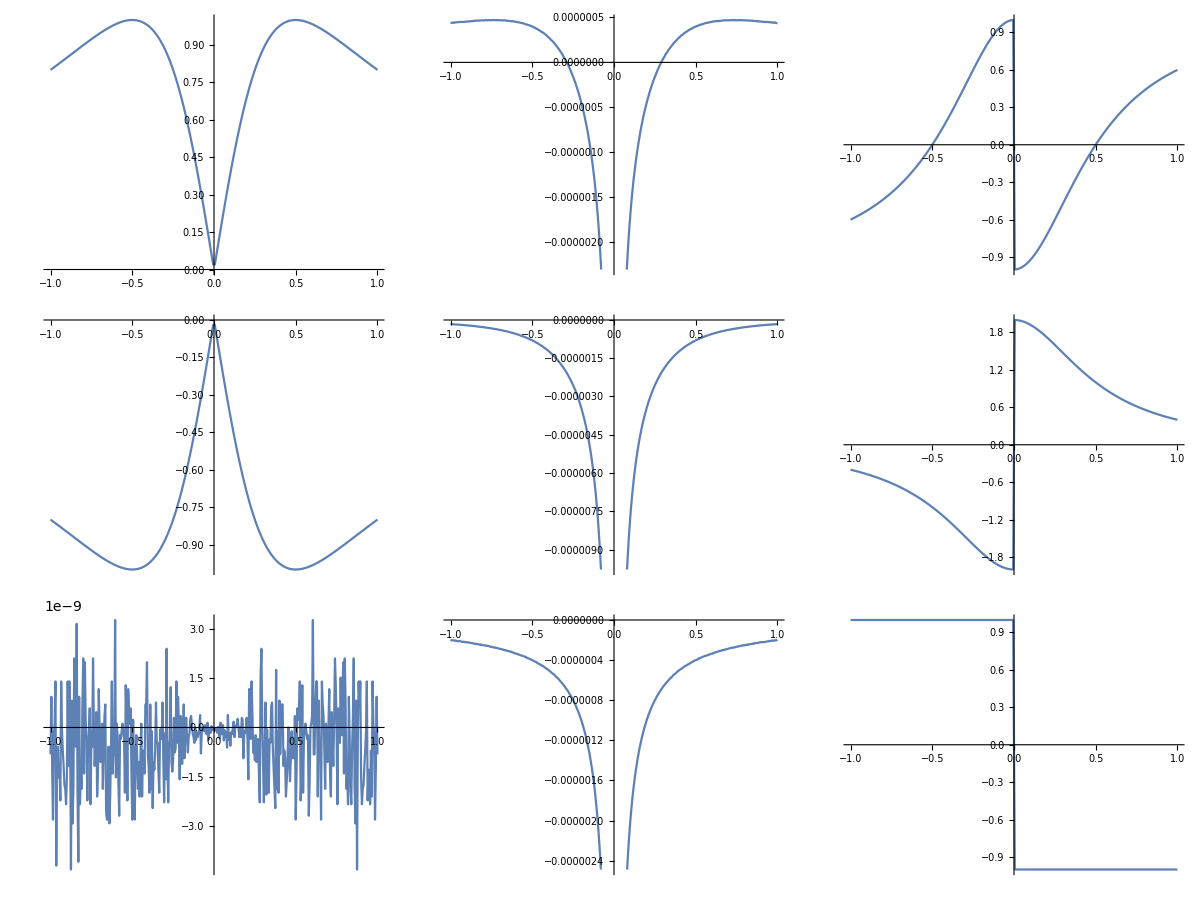

```mathematica
Block[{struct, g=DeleteCases[0.]@Range[-1.0*^-0, 1.0*^-0, 5.0*^-3]},
Table[
struct={
{-.5, .7, 0},
{0, .7, x},
{.5, .7, 0}
};
getAngleFD[struct, 1, 2, 3]//Partition[#, 3]&,
{x, g}
]//Transpose[#, {3, 1, 2}]&
//Map[ListLinePlot[Transpose[{g, #}], ImageSize->220]&, #, {2}]&//Grid
]
```

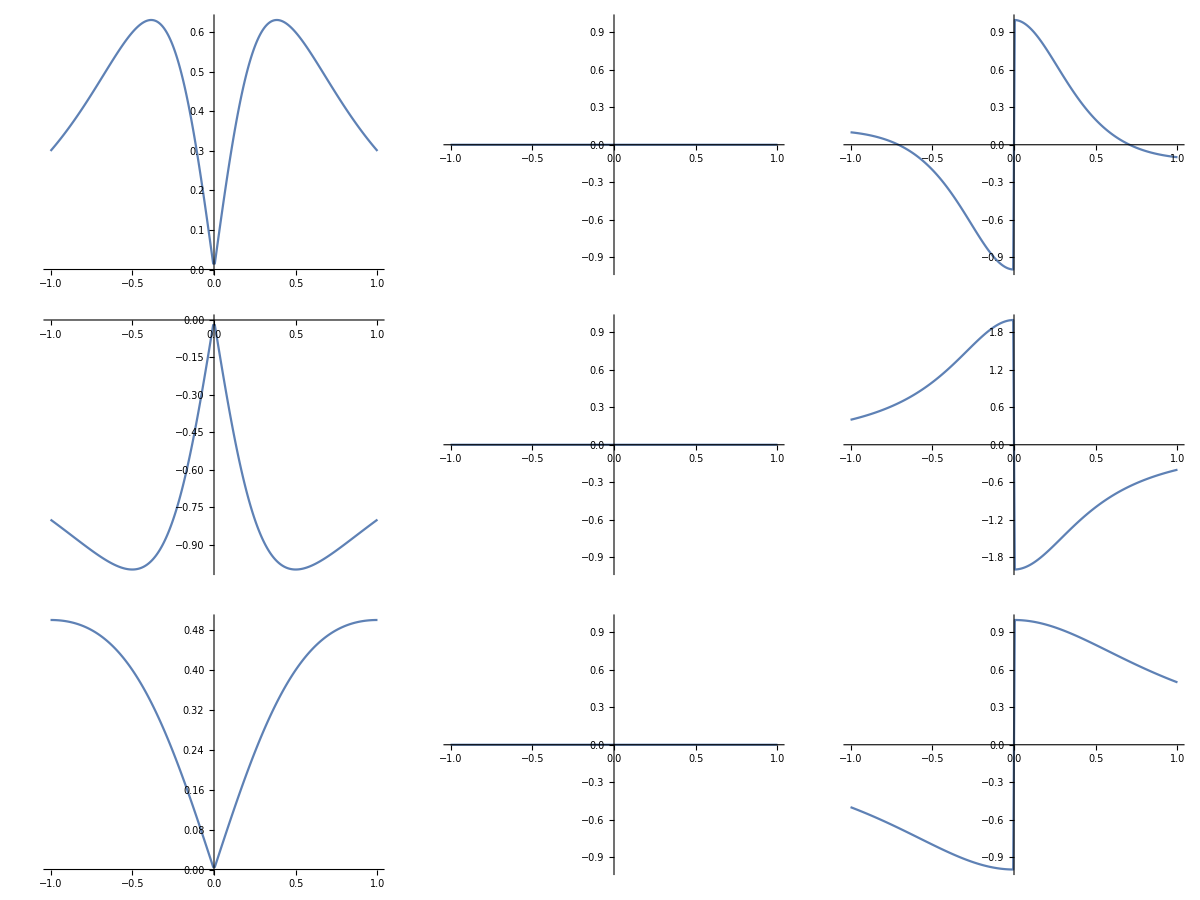

```mathematica
Block[{struct, g=DeleteCases[0.]@Range[-1.0*^-0, 1.0*^-0, 5.0*^-3]},
Table[
struct={
{-.5, .7, x},
{0., .7, 0.},
{.5, .7, 0.}
};
testAngleDerivs2[struct, 1, 2, 3],
{x, g}
]//Transpose[#, {3, 1, 2}]&
//Map[ListLinePlot[Transpose[{g, #}], ImageSize->220]&, #, {2}]&//Grid
]
```

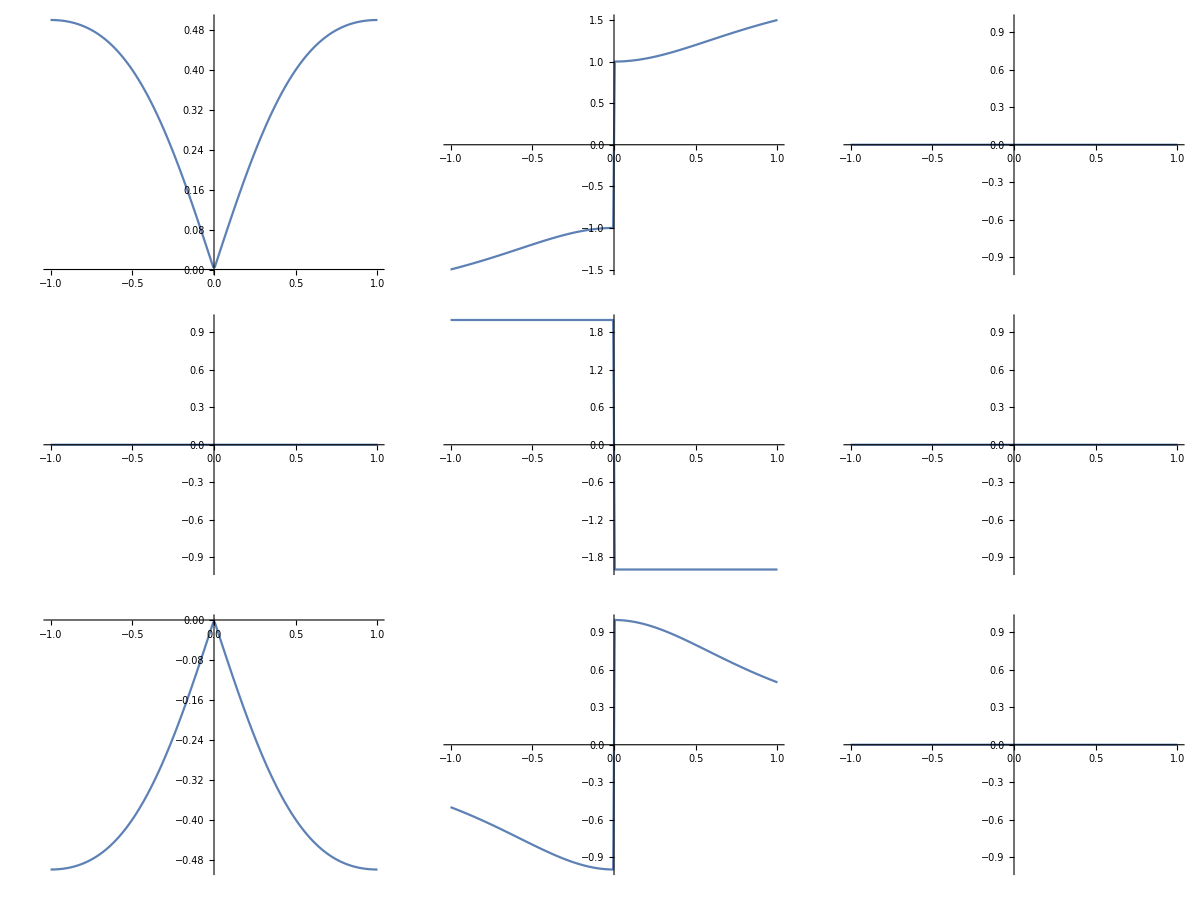

```mathematica
Block[{struct, g=DeleteCases[0.]@Range[-1.0*^-0, 1.0*^-0, 5.0*^-3]},
Table[
struct={
{-.5, .7, 0.},
{0., .7, 0.},
{.5, .7+x, 0.}
};
testAngleDerivs2[struct, 1, 2, 3],
{x, g}
]//Transpose[#, {3, 1, 2}]&
//Map[ListLinePlot[Transpose[{g, #}], ImageSize->220]&, #, {2}]&//Grid
]
```

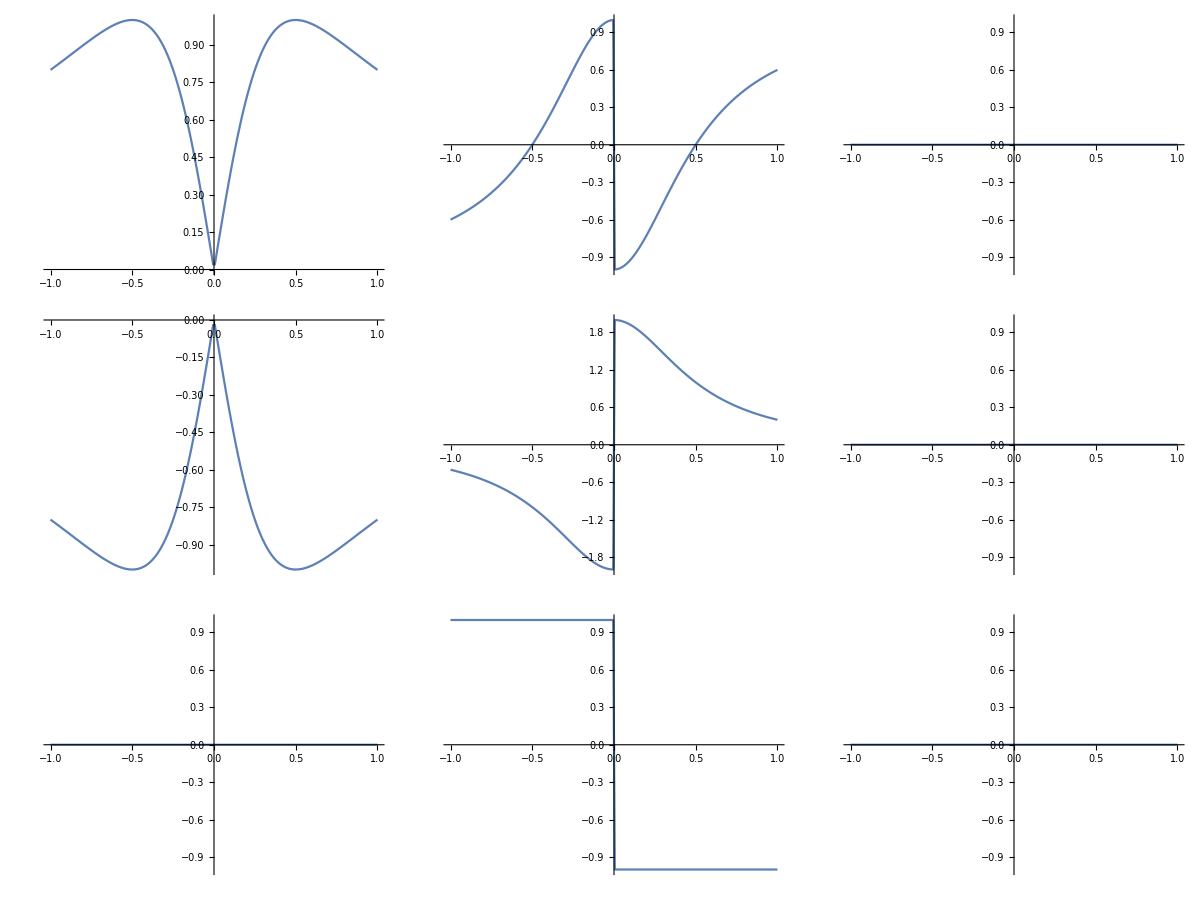

```mathematica
Block[{struct, g=DeleteCases[0.]@Range[-1.0*^-0, 1.0*^-0, 5.0*^-3]},
Table[
struct={
{-.5, .7, 0.},
{0., .7+x, 0.},
{.5, .7, 0.}
};
testAngleDerivs2[struct, 1, 2, 3],
{x, g}
]//Transpose[#, {3, 1, 2}]&
//Map[ListLinePlot[Transpose[{g, #}], ImageSize->220]&, #, {2}]&//Grid
]
```

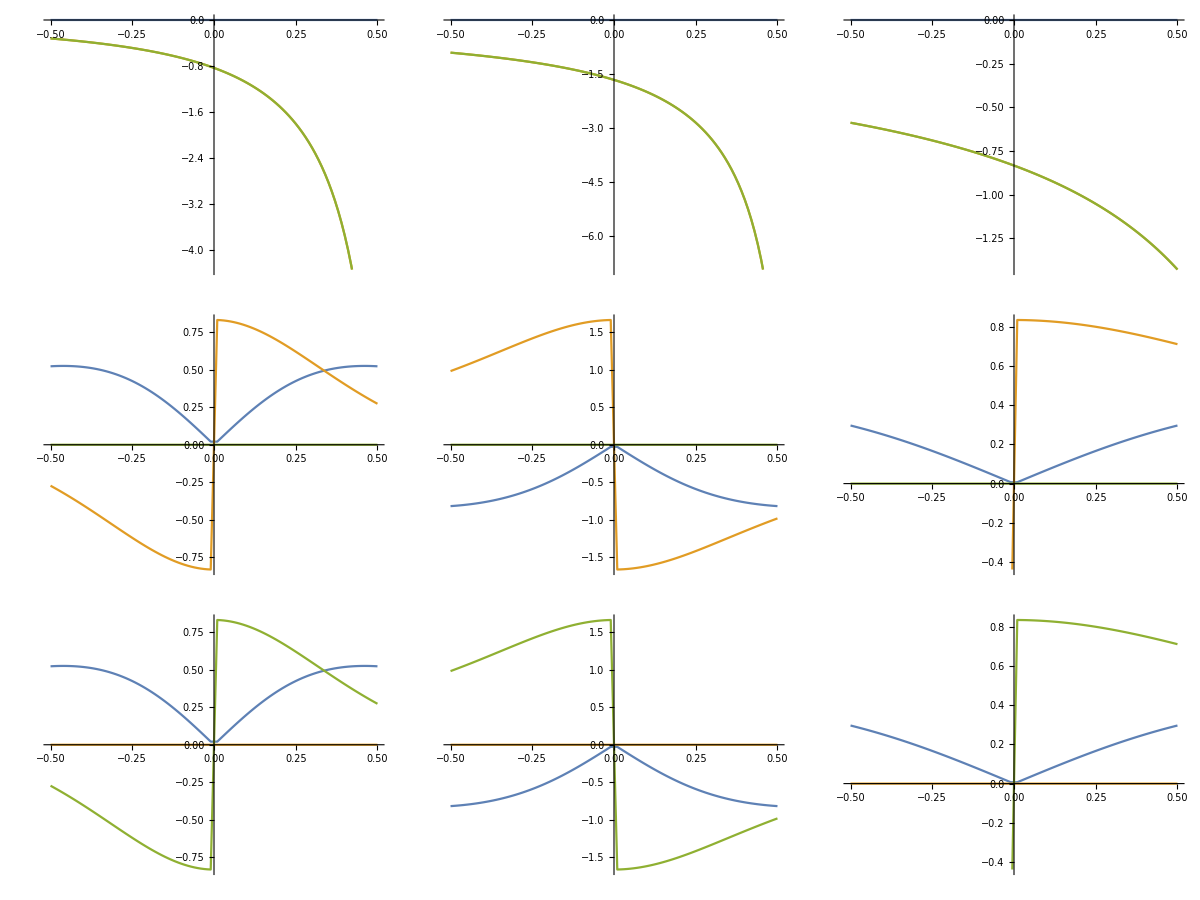
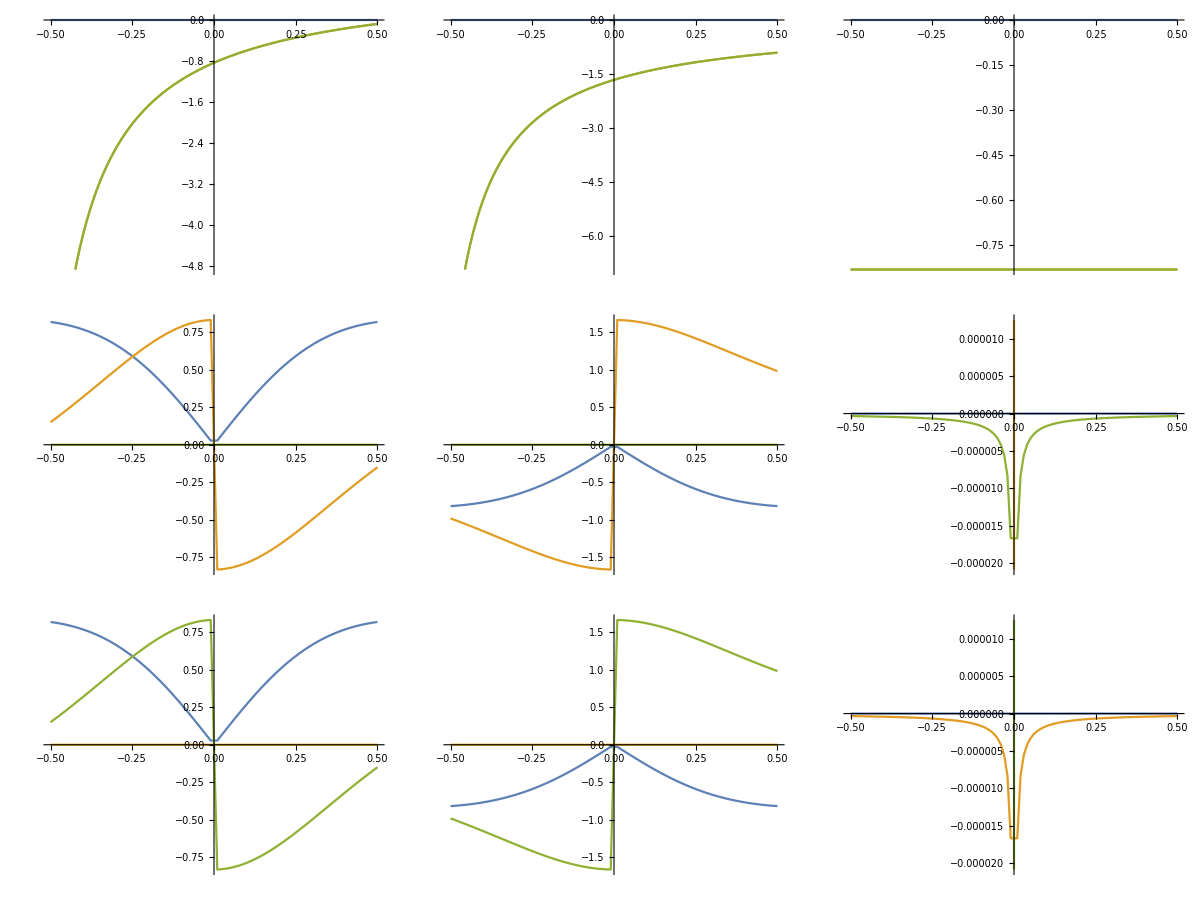
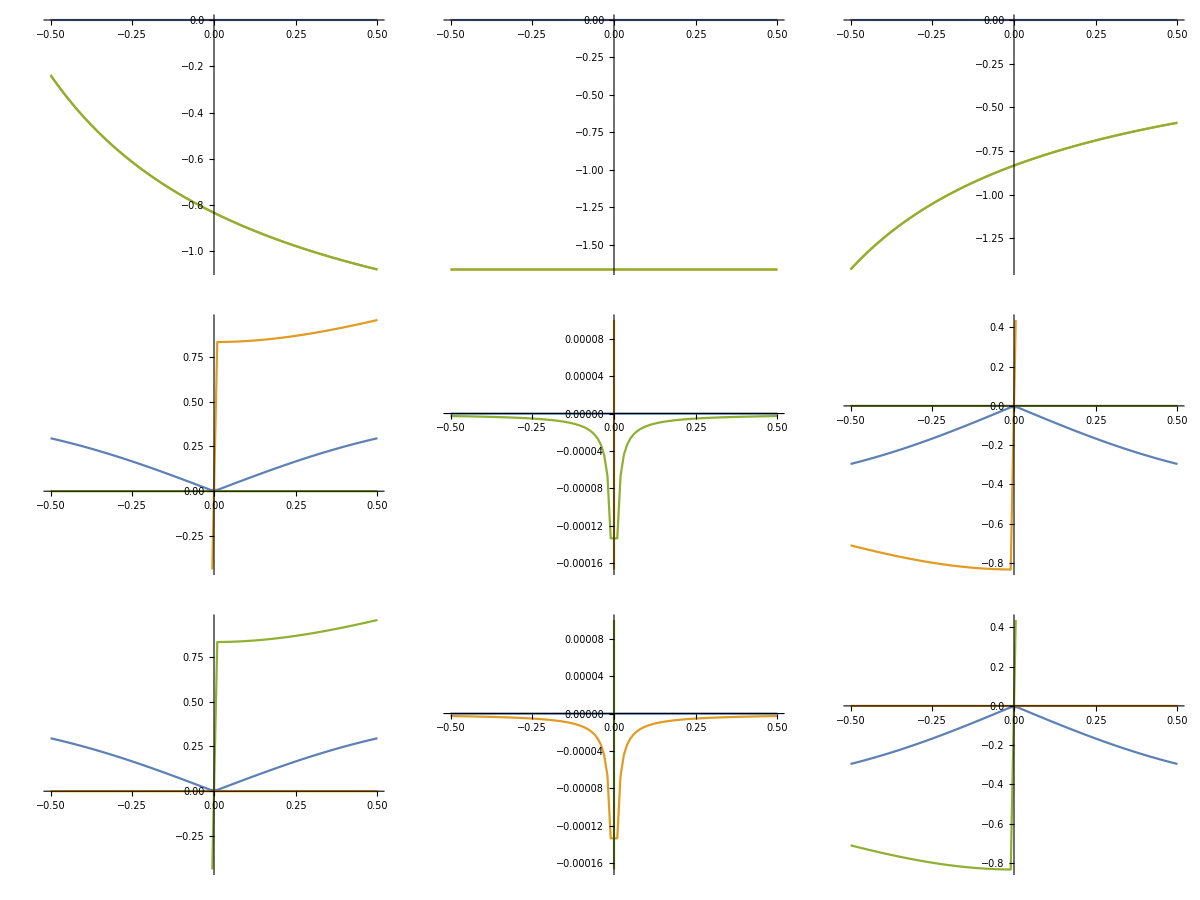

```mathematica
Block[{baseStruct, struct, g=DeleteCases[0.]@Range[-5.0*^-1, 5.0*^-1, 1.0*^-2]},
baseStruct={
{-.6, .7, 0.},
{0., .7, 0.},
{.6, .7, 0.}
};
Table[
struct=ReplacePart[baseStruct, {i, j}-> baseStruct[[i, j]]+x];
getAngleFD[struct, 1, 2, 3]//Partition[#, 3]&,
{x, g},
{i, 3},
{j, 3}
]//Transpose[#, {5, 1, 2, 3, 4}]&
//Map[ListLinePlot[Transpose[{g, #}]&/@#, ImageSize->220]&, #, {3}]&
]//Map[Grid]
```

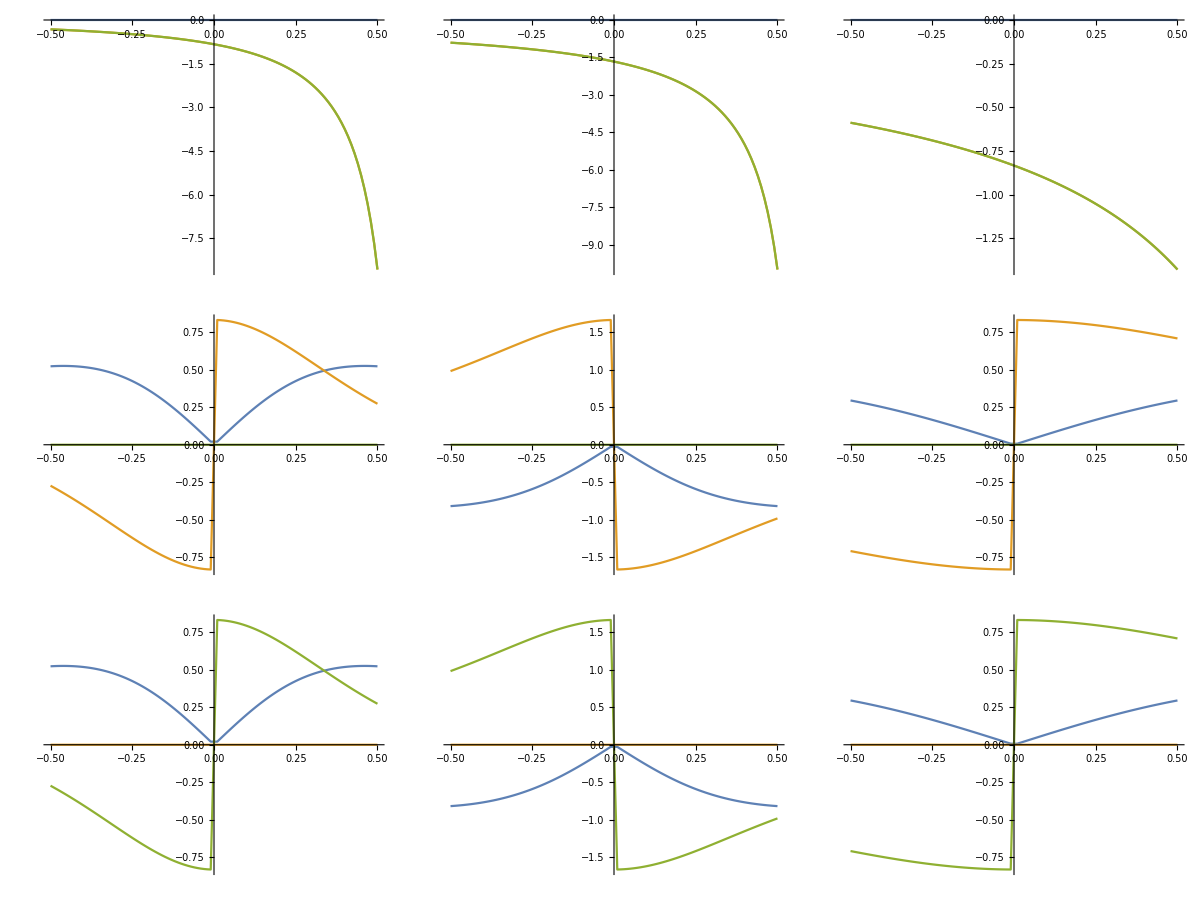
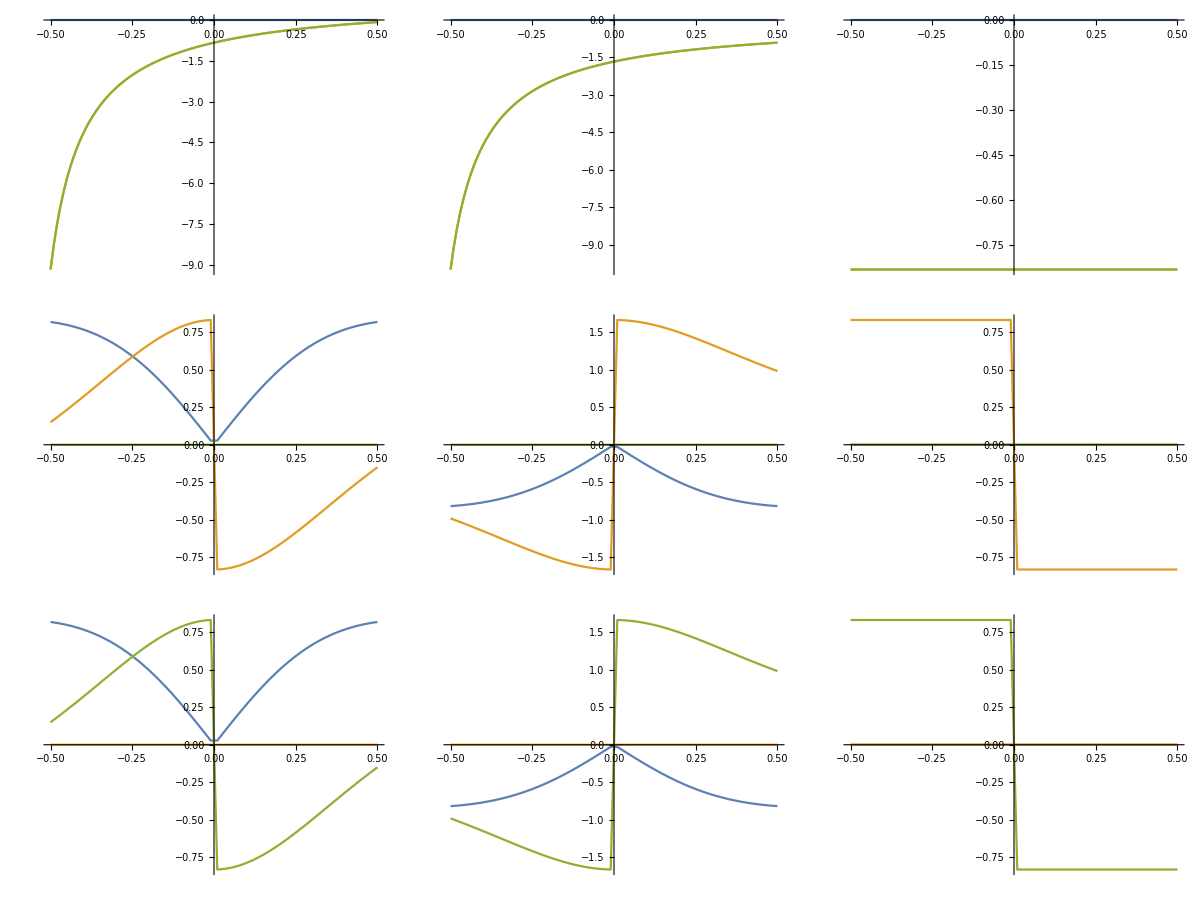
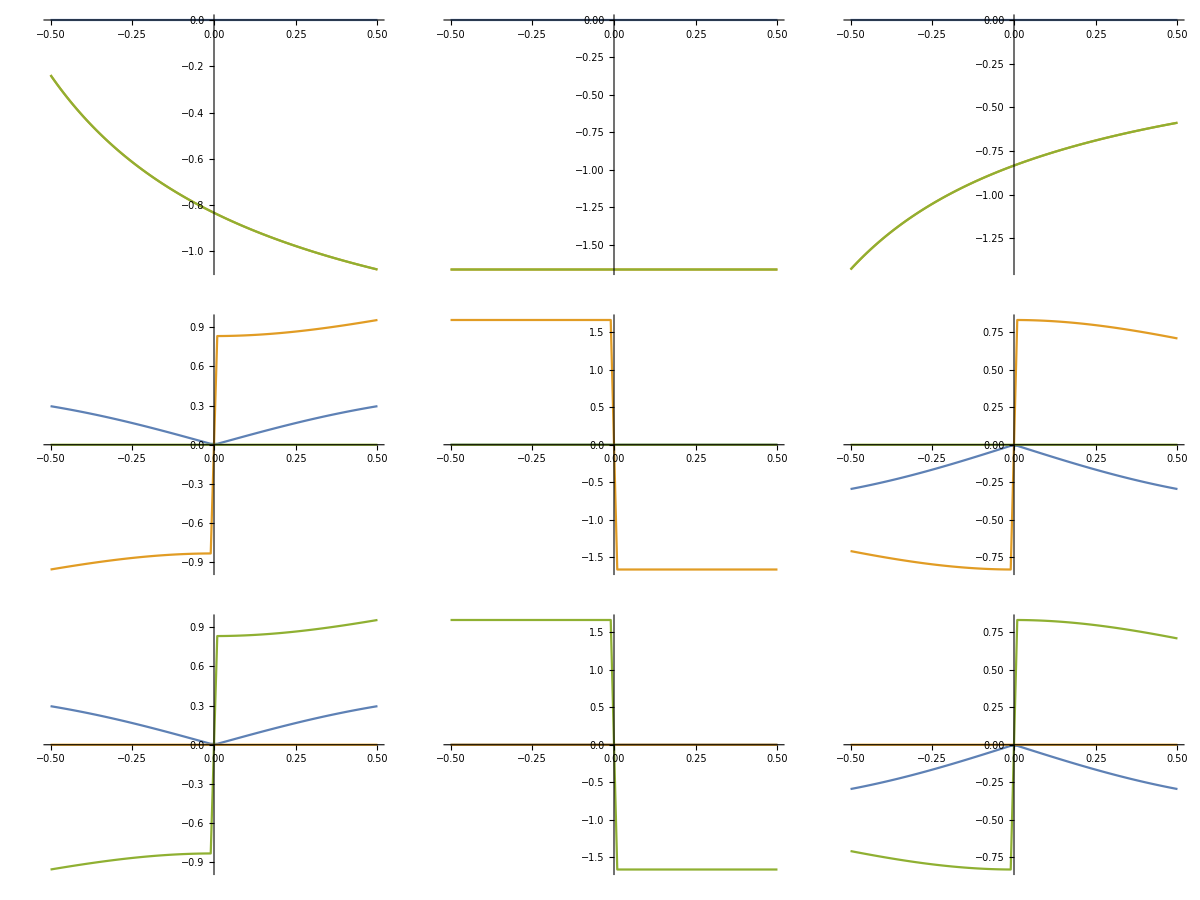

```mathematica
Block[{baseStruct, struct, g=DeleteCases[0.]@Range[-5.0*^-1, 5.0*^-1, 1.0*^-2]},
baseStruct={
{-.6, .7, 0.},
{0., .7, 0.},
{.6, .7, 0.}
};
Table[
struct=ReplacePart[baseStruct, {i, j}-> baseStruct[[i, j]]+x];
testAngleDerivs2[struct, 1, 2, 3],
{x, g},
{i, 3},
{j, 3}
]//Transpose[#, {5, 1, 2, 3, 4}]&
//Map[ListLinePlot[Transpose[{g, #}]&/@#, PlotRange->All, ImageSize->220]&, #, {3}]&
]//Map[Grid]//Column
```

#### Second Derivatives

These derivatives are relatively straight-forward extensions of the firsts. We’ll start with the derivatives in a again

∂^2/(∂a∂a)sin(a, b) =∂/(∂a)1/(|a|)(b̂×n̂-sin(a, b)â)
=(∂/(∂a)1/(|a|))(b̂×n̂-sin(a, b)â)+1/(|a|)(b̂×∂/(∂a)n̂-(∂/(∂a)sin(a, b))â-sin(a, b)∂/(∂a)â)
∂^2/(∂a∂a)cos(a, b) =∂/(∂a)1/(|a|)(b̂-cos(a, b)â)
=(∂/(∂a)1/(|a|))(b̂-cos(a, b)â)-1/(|a|)((∂/(∂a)cos(a, b))â+cos(a, b)∂/(∂a)â)
∂^2/(∂a∂b)sin(a, b) =∂/(∂a)1/(|b|)(n̂×â-sin(a, b)b̂)
=1/(|b|)(∂/(∂a)n̂×â-(∂/(∂a)sin(a, b))b̂)
∂^2/(∂a∂b)cos(a, b) =∂/(∂a)1/(|b|)(â-cos(a, b)b̂)
=1/(|b|)((∂â)/(∂a)-(∂/(∂a)cos(a, b))b̂)

And then we’ll take these on one-by-one to manage the complexity. The first sin term is pretty straightforward

∂^2/(∂a∂a)sin(a, b) =∂/(∂a)1/(|a|)(b̂×n̂-sin(a, b)â)
=(∂/(∂a)1/(|a|))(b̂×n̂-sin(a, b)â)+1/(|a|)(b̂×∂/(∂a)n̂-(∂/(∂a)sin(a, b))â-sin(a, b)∂/(∂a)â)
=-(1/(|a|)^2(∂|a|)/(∂a))⊗(b̂×n̂-sin(a, b)â)+1/(|a|)(b̂×((∂n)/(∂a)(∂n̂)/(∂n))-(∂sin(a, b))/(∂a)⊗â-sin(a, b)(∂â)/(∂a))
=(-1/(|a|)â⊗(∂sin(a, b))/(∂a))+1/(|a|)(b̂×((∂n)/(∂a)(∂n̂)/(∂n))-(∂sin(a, b))/(∂a)⊗â-sin(a, b)(∂â)/(∂a))
=-1/(|a|)((∂sin(a, b))/(∂a)⊗â + â⊗(∂sin(a, b))/(∂a) + sin(a, b)(∂â)/(∂a) - b̂×((∂n)/(∂a)(∂n̂)/(∂n)))

where the only new term is (∂n)/(∂a) but we’ve actually done that implicitly before. We won’t expand this all out, but we will look at one interesting term

b̂×((∂n)/(∂a)(∂n̂)/(∂n))=b̂×(((∂a)/(∂a)×b)(∂|n|)/(∂n^2))
=( b̂ × ((𝕀_3×b)(∂^2 |n|)/(∂n^2))_1
b̂ × ((𝕀_3×b)(∂^2 |n|)/(∂n^2))_2
b̂ × ((𝕀_3×b)(∂^2 |n|)/(∂n^2))_3 )
=-( b̂ × ((𝕀_3×b)(∂^2 |n|)/(∂n^2))_1
b̂ × ((𝕀_3×b)(∂^2 |n|)/(∂n^2))_2
b̂ × ((𝕀_3×b)(∂^2 |n|)/(∂n^2))_3 )
=-(ϵ_3 b)(∂^2 |n|)/(∂n^2)(ϵ_3 b̂)

it’s unclear which form will be easier for extensions, but this is potentially nicer for implementation. One thing worth noting is that (∂^2 |n|)/(∂n^2) is potentially bad numerically, since when a and b are colinear the cross-product vector is zero and the second derivative of the norm

Next is the cos term

∂^2/(∂a∂a)cos(a, b) =∂/(∂a)1/(|a|)(b̂-cos(a, b)â)
=(∂/(∂a)1/(|a|))⊗(b̂-cos(a, b)â) + 1/(|a|)(∂/(∂a)b̂ -∂/(∂a)(cos(a, b)â))
=(∂/(∂a)1/(|a|))⊗(b̂-cos(a, b)â) - 1/(|a|)((∂cos(a, b))/(∂a)⊗â + cos(a, b) (∂â)/(∂a)))
=(-1/(|a|)^2(∂|a|)/(∂a))⊗(b̂-cos(a, b)â) - 1/(|a|)((∂cos(a, b))/(∂a)⊗â + cos(a, b) (∂â)/(∂a))
=-1/(|a|)( 1/(|a|)(∂|a|)/(∂a)⊗(b̂-cos(a, b)â) +(∂cos(a, b))/(∂a)⊗â + cos(a, b) (∂â)/(∂a))
=-1/(|a|)((∂|a|)/(∂a)⊗(∂cos(a, b))/(∂a) + (∂cos(a, b))/(∂a)⊗â + cos(a, b) (∂â)/(∂a))
=-1/(|a|)(â⊗(∂cos(a, b))/(∂a) + (∂cos(a, b))/(∂a)⊗â + cos(a, b) (∂â)/(∂a))
=-1/(|a|)((∂|a|)/(∂a)⊗(∂cos(a, b))/(∂a) + (∂cos(a, b))/(∂a)⊗(∂|a|)/(∂a) + cos(a, b) (∂^2 |a|)/(∂a^2))

and onto the mixed sin term

∂^2/(∂a∂b)sin(a, b)=1/(|b|)(∂/(∂a)n̂×â-(∂/(∂a)sin(a, b))b̂)
=1/(|b|)((∂n̂)/(∂a)×â+n̂×(∂â)/(∂a)-(∂sin(a, b))/(∂a)⊗b̂)
=1/(|b|)(((∂n)/(∂a)(∂n̂)/(∂n))×â+(n̂×(∂â)/(∂a))-(∂sin(a, b))/(∂a)⊗b̂)

where,

((∂n)/(∂a)(∂n̂)/(∂n))×â=–â×((∂n)/(∂a)(∂n̂)/(∂n))
=(ϵ_3 b)(∂^2 |n|)/(∂n^2)(ϵ_3 â)
n̂×(∂â)/(∂a)=(∂â)/(∂a)(ϵ_3 n̂)

and mixed cos term

∂^2/(∂a∂b)cos(a, b) =∂/(∂a)1/(|b|)(â-cos(a, b)b̂)
=1/(|b|)((∂â)/(∂a)-(∂/(∂a)cos(a, b))b̂)
=1/(|b|)((∂â)/(∂a)-(∂cos(a, b))/(∂a)⊗b̂)

These are eminently doable and just build off of the identities we had from before.

We then should deal with the normal derivative, which is pretty simple

(∂n)/(∂a)=(∂a)/(∂a)×b

and at this point we’ve got everything we need to make these second derivatives.

The derivatives in b will basically differ only up to some commutativity/transpose stuff.

##### Angles

For the second derivative of the angle we have

∂^2/(∂β∂α)θ(a, b) =∂/(∂β) (cos(a, b)∂/(∂α)sin(a, b) - sin(a, b)∂/(∂α)cos(a, b))
=∂/(∂β)cos(a, b)∂/(∂α)sin(a, b)+cos(a, b)∂/(∂β∂α)sin(a, b)-∂/(∂β)sin(a, b)∂/(∂α)cos(a, b)-sin(a, b)∂/(∂β∂α)cos(a, b)

and again we can build all of this from what we had before.

## Embedded Internal Derivatives

It turns out that the Cartesian coordinates we generate are actually expected to be referenced to the Eckart frame...where this is made explicit I don’t know.

This means we actually generate coordinates like

X_O=zmtocart(internals)
X=Ek(X_O, ref)·(X_O-COM(X_O))

and so when we take derivatives of this we have

∂/(∂r)X=(∂ Ek(X_O, ref))/(∂r)·(X_O-COM(X_O)) +Ek(X_O, ref)·(∂/(∂r)X_O - ∂/(∂r)COM(X_O))

and I can already evaluate

∂/(∂r)X_O

and from this it’s relatively straightforward to evaluate

∂/(∂r)COM(X_O)

so then the question is what can be done about

(∂ Ek(X_O, ref))/(∂r)

for that we’ll use the definition that

U, P = pd ∑_i m_i/M_T(X_O)_i⊗(ref)_i
Ek(X_O, ref)=U

where pd is the polar decomposition, defined for a real symmetric matrix by

P=(A^T A)^(1/2)
U=A P^-1

which gives us the relation

A = ∑_i m_i/M_T(X_O)_i⊗(ref)_i
Ek(X_O, ref) = (A(A^T A))^(-1/2)

Much of this is straightforwardly differentiable...but (A^T A)^(-1/2) is a challenge. It’s formally defined by first diagonalizing A^T A to get

A^T A=QD Q^-1

and then

(A^T A)^(-1/2)=Q D^(-1/2)Q^-1

where

(D^(-1/2))_ij=λ_i^(-1/2)δ_ij

the issue now is that we need explicit algebraic forms for λ_i and Q if we want to differentiate this...

Because of this, it seems like the easiest approach might be to write

(∂ Ek(X_O, ref))/(∂r)=(∂X_O)/(∂r)(∂ Ek(X_O, ref))/(∂X_O)

and then numerically evaluate

(∂ Ek(X_O, ref))/(∂X_O)

since direct numerical evaluation of

(∂ Ek(X_O, ref))/(∂r)

will be slowed by the need to transform to Cartesian coordinates for each displacement in r